## Paths and Includes

```mathematica
SetOptions[$FrontEnd,"CommonDefaultFormatTypes"->{"Output"->StandardForm}]
basepath=$HomeDirectory<>"/sivers_TMD_PhD_project/mathematica_hari"
SetDirectory[basepath<>"/output"];
includepath=basepath<>"/include";
AppendTo[$Path, includepath];
Needs["LatticeAnalysis`"];
 <<"LatticeAnalysis`"
(* do not keep track of intermediate results *)
$HistoryLength=0;
```

/Users/hariprashadravikumar/sivers_TMD_PhD_project/mathematica_hari

## Configuration

We must provide information about the lattice spacing of the ensemble ourselves; it is not in the data base files (obviously)

```mathematica
Needs["FourierSeries`"]
lata=0.11403
```

0.11403

## Open Database

open the BIDATEX data base with the correlator data

```mathematica
AmpDB = BIDATEXReader["/Users/hariprashadravikumar/sivers_TMD_PhD_project/sivers_new/newDBforA12BA2B/db_Alleta_correct_try_A12B_A2B_bL_bT_bevenodd.bidatex"]
AmpDBPbbsq = BIDATEXReader["/Users/hariprashadravikumar/sivers_TMD_PhD_project/sivers_new/newDBforA12BA2B/db_Alleta_correct_try_A12B_A2B_Pb32by2Pi_bsq_bevenodd.bidatex"]
```

< -MemDB- {A,bL,bNum,bT,data,EN,etav,MN,PL,zta}>

< -MemDB- {A,bNum,bsquare,data,EN,etav,MN,Pb32by2Pi,PL,zta}>

```mathematica
MemDBGet[AmpDBPbbsq,MemDBSelect[AmpDBPbbsq,{A->A12B,PL->-4,etav->8, bNum->odd}],{bsquare, Pb32by2Pi}]//Union
```

{{1,0},{2,-4},{2,4},{4,0},{5,-8},{5,-4},{5,4},{5,8},{8,-8},{8,8},{9,0},{16,0},{17,-16},{17,16},{18,-12},{18,12},{20,-16},{20,-8},{20,8},{20,16},{25,0},{32,-16},{32,16},{36,0},{45,-24},{45,-12},{45,12},{45,24},{49,0},{50,-20},{50,20},{68,-32},{68,32}}

```mathematica
(* SAVE TO H5 FOR PySR*)
(*PbbsqA2Bvalueserrbars[ampname_,P1_,etavalue_]:=(
PbbsqA2BvalueerrbarLIST={};
PbaveragedbsquareA2B=MemDBGet[AmpDBPbbsq,MemDBSelect[AmpDBPbbsq,{A->ampname,PL->P1,etav->etavalue, bNum->odd}],{Pb32by2Pi, bsquare,data}];
forMakeErrBars = {};
Do[
AppendTo[forMakeErrBars,{{PbaveragedbsquareA2B[[i]][[1]],PbaveragedbsquareA2B[[i]][[2]]},PbaveragedbsquareA2B[[i]][[3]]}],{i, Length[PbaveragedbsquareA2B]}];
PbbsqA2Bvalueerrbar = MakeErrBars[forMakeErrBars];
Do[
AppendTo[PbbsqA2BvalueerrbarLIST, {etavalue, PbbsqA2Bvalueerrbar[[i]][[1]][[1]][[1]] ,PbbsqA2Bvalueerrbar[[i]][[1]][[1]][[2]],  PbbsqA2Bvalueerrbar[[i]][[1]][[2]],  PbbsqA2Bvalueerrbar[[i]][[2]][[1]][[2]]}];
,{i, Length[PbbsqA2Bvalueerrbar]}];
Return[PbbsqA2BvalueerrbarLIST]
)
ExporttoH5Amp[ampname_,P1_]:=(
Export["/Users/hariprashadravikumar/sivers_TMD_PhD_project/save_h5_A12B_A2B/allPL_eta_bP_bsq_mean_err__forReImAmps.h5",Table["Pl"<>ToString[P1]<>"/eta_"<>ToString[n]<>"_bP_bsq_Im"<>ToString[ampname]<>"_err"->PbbsqA2Bvalueserrbars[ampname, P1, n],{n,0,10}],OverwriteTarget->"Append"];
)
Do[ExporttoH5Amp[A2B,-i],{i, 1,4}]*)
```

```mathematica
Import["/Users/hariprashadravikumar/sivers_TMD_PhD_project/save_h5_A12B_A2B/allPL_eta_bP_bsq_mean_err_forReImAmps.h5","StructureGraph"]
```

-Graphics-

```mathematica
PlotAbLfordiffbLbT[ampname_,P1_, etavalue_, bnum_, Nnum_]:=(
Print[Nnum ampname," =>  = ",P1," ,eta = ", etavalue];
bTlist= Union[MemDBGet[AmpDB,MemDBSelect[AmpDB,{A->ampname,PL->P1,etav->etavalue, bNum->bnum}],bT]];
bLlist= Union[MemDBGet[AmpDB,MemDBSelect[AmpDB,{A->ampname,PL->P1,etav->etavalue, bNum->bnum}],bL]];
PlotbLforDiffbTList={};
Do[
bLAmp=MemDBGet[AmpDB,MemDBSelect[AmpDB,{A->ampname,PL->P1,etav->etavalue,bT->bTi, bNum->bnum}],{bL,data}];
AppendTo[PlotbLforDiffbTList,bLAmp];
 ,{bTi,bTlist}];
PlotbL= ErrorListPlot[Table[MakeErrBars[PlotbLforDiffbTList[[bTi]]],{bTi, Length[bTlist]}],FrameLabel->{, Nnum ampname }, Frame->True ,PlotRange->Full,PlotLegends->Table[" = "<>ToString[bTlist[[bTi]]],{bTi,Length[bTlist]}], ImageSize->450];
Export["/Users/hariprashadravikumar/Downloads/bL_"<>ToString[ampname]<>"_b_"<>ToString[bnum]<>"_P1_"<>ToString[P1]<>"_eta_"<>ToString[etavalue]<>".pdf",PlotbL,"PDF",ImageResolution->600];
PlotbTforDiffbLList={};
Do[
bLAmp=MemDBGet[AmpDB,MemDBSelect[AmpDB,{A->ampname,PL->P1,etav->etavalue,bL->bLi, bNum->bnum}],{bT,data}];
AppendTo[PlotbTforDiffbLList,bLAmp];
 ,{bLi,bLlist}];
PlotbT= ErrorListPlot[Table[MakeErrBars[PlotbTforDiffbLList[[bLi]]],{bLi, Length[bLlist]}],FrameLabel->{,ampname b bnum}, Frame->True ,PlotRange->Full,PlotLegends->Table[" = "<>ToString[bLlist[[bLi]]],{bLi,Length[bLlist]}], ImageSize->450];
Export["/Users/hariprashadravikumar/Downloads/bT_"<>ToString[ampname]<>"_b_"<>ToString[bnum]<>"_P1_"<>ToString[P1]<>"_eta_"<>ToString[etavalue]<>".pdf",PlotbT,"PDF",ImageResolution->600];GraphicsRow[{PlotbL,PlotbT},ImageSize->Full]
)
PlotAfordiffBPbbsq[ampname_,P1_, etavalue_, bnum_, Nnum_]:=(
Print[Nnum ampname," =>  = ",P1," ,eta = ", etavalue];
bsquarelist= Union[MemDBGet[AmpDBPbbsq,MemDBSelect[AmpDBPbbsq,{A->ampname,PL->P1,etav->etavalue, bNum->bnum}],bsquare]];
(*bsquarelist = Select[fullbsquarelist,8<=#<=25&];*)
Pb32by2Pilist= Union[MemDBGet[AmpDBPbbsq,MemDBSelect[AmpDBPbbsq,{A->ampname,PL->P1,etav->etavalue, bNum->bnum}],Pb32by2Pi]];
PlotPbforDiffbsq={};
Do[
PbAmp=MemDBGet[AmpDBPbbsq,MemDBSelect[AmpDBPbbsq,{A->ampname,PL->P1,etav->etavalue,bsquare->bsqi, bNum->bnum}],{Pb32by2Pi,data}];
AppendTo[PlotPbforDiffbsq,PbAmp];
 ,{bsqi,bsquarelist}];
PlotbP= ErrorListPlot[Table[MakeErrBars[PlotPbforDiffbsq[[bsqi]]],{bsqi, Length[bsquarelist]}],FrameLabel->{ , Nnum ampname }, Frame->True ,PlotRange->Full,PlotLegends->Table[" = "<>ToString[bsquarelist[[bsqi]]],{bsqi,Length[bsquarelist]}], ImageSize->450];
Export["/Users/hariprashadravikumar/Downloads/bP_"<>ToString[ampname]<>"_b_"<>ToString[bnum]<>"_P1_"<>ToString[P1]<>"_eta_"<>ToString[etavalue]<>".pdf",PlotbP,"PDF",ImageResolution->600];
PlotbsqforDiffPb={};
Do[
bsqAmp=MemDBGet[AmpDBPbbsq,MemDBSelect[AmpDBPbbsq,{A->ampname,PL->P1,etav->etavalue,Pb32by2Pi->Pbi, bNum->bnum}],{bsquare,data}];
AppendTo[PlotbsqforDiffPb,bsqAmp];
 ,{Pbi,Pb32by2Pilist}];
Plotbsq= ErrorListPlot[Table[MakeErrBars[PlotbsqforDiffPb[[Pbi]]],{Pbi, Length[Pb32by2Pilist]}],FrameLabel->{,Nnum ampname }, Frame->True ,PlotRange->Full,PlotLegends->Table[" = "<>ToString[Pb32by2Pilist[[Pbi]]],{Pbi,Length[Pb32by2Pilist]}], ImageSize->450];
Export["/Users/hariprashadravikumar/Downloads/bsq_"<>ToString[ampname]<>"_b_"<>ToString[bnum]<>"_P1_"<>ToString[P1]<>"_eta_"<>ToString[etavalue]<>".pdf",Plotbsq,"PDF",ImageResolution->600];
GraphicsRow[{PlotbP,Plotbsq},ImageSize->Full]
)
```

```mathematica
PlotAbLfordiffbLbT[A2B,-1,8, odd, "Im"]
```

Im A2B =>  = -1 ,eta = 8

-Graphics-

```mathematica
PlotAfordiffBPbbsq[A12B,-1,10, even, "Re"]
```

Re A12B =>  = -1 ,eta = 10

-Graphics-

```mathematica
modelfitJackkife[model_, fitParams_, x_, y_]:=Module[{numFs, modelvaluej,modelvalue, jackknifeResults},
numFs=Length[fitParams[[1]]];
modelvaluej[j_]:=Module[{datafitParams},
datafitParams={fitParams[[1]][[j]],fitParams[[2]][[j]],fitParams[[3]][[j]]};
model[x,y,datafitParams]
];
modelvalue=Table[modelvaluej[j],{j,numFs}];
jackknifeResults=JacknifeSamples@@(modelvalue);
jackknifeResults
];
meanfromJK[JKvalue_]:=Module[{meanvalue},
meanvalue = MakeErrBars[{{1,JKvalue}}][[1]][[1]][[2]];
meanvalue
];
errorfromJK[JKvalue_]:=Module[{errorvalue},
errorvalue = MakeErrBars[{{1,JKvalue}}][[1]][[2]][[1]][[2]];
errorvalue
];
chisqOEsigmasq[O_, E_]:=Module[{OEsigmasq, Omean,Emean, Esigmasq, Osigmasq, sigmasqTotal},
Omean=meanfromJK[O];
Emean=meanfromJK[E];
Esigmasq = (MakeErrBars[{{1,E}}][[1]][[2]][[1]][[2]])^2;
Osigmasq = (MakeErrBars[{{1,O}}][[1]][[2]][[1]][[2]])^2;
sigmasqTotal = Esigmasq+Osigmasq;
OEsigmasq = If[sigmasqTotal==0,0,((Omean-Emean)^2)/sigmasqTotal];
OEsigmasq
];

JackknifeFit3D[xyJKf_,model_,para_,vari_, modelFnName_]:=Module[
{numFs,fitParamsForFj,fitParamsList,paramLists,jackknifeResults,DoF, chisquare, observed, expected, chisquareperDoF},
numFs=Length[xyJKf[[1,3]]];
WeightList = {};
Do[
ε=10^-6;
σ=(MakeErrBars[{{1,xyJKf[[ii]][[3]]}}][[1]][[2]][[1]][[2]]);
AppendTo[WeightList,1/Max[σ,ε]^2], {ii, Length[xyJKf]}];
(*Function to extract j-th f values and fit them*)
fitParamsForFj[j_]:=Module[{data,fit},
data={#[[1]],#[[2]],#[[3,j]]}&/@xyJKf;(*Extract f_j values*)
fit=NonlinearModelFit[data,model,para,vari, Weights->WeightList,Method->{"LevenbergMarquardt"}];
fit["BestFitParameters"] (*Extract fitted parameters*)
];
(*Compute fit parameters for each f_j*)
fitParamsList=Table[fitParamsForFj[j],{j,numFs}];
jackknifeResults=Table[JacknifeSamples@@(para[[pa]]/. fitParamsList),{pa,Length[para]}];
DoF=Length[xyJKf];
chisquare=0;
Do[
observed = modelfitJackkife[modelFnName, jackknifeResults, xyJKf[[i]][[1]], xyJKf[[i]][[2]]];
expected= xyJKf[[i]][[3]];
chisquare = chisquare + chisqOEsigmasq[observed, expected];
,{i,DoF}];
chisquareperDoF=chisquare/(DoF-3);
{FitParameters->jackknifeResults, chisquareDoF->chisquareperDoF}];
```

```mathematica
modelfitJackkifband[model_, fitParams_,fixedVare_, x_]:=Module[{numFs, modelvaluej,modelvalue, jackknifeResults},
numFs=Length[fitParams[[1]]];
modelvaluej[j_]:=Module[{datafitParams},
datafitParams={fitParams[[1]][[j]],fitParams[[2]][[j]],fitParams[[3]][[j]]};
model[x, fixedVare,datafitParams]
];
modelvalue=Table[modelvaluej[j],{j,numFs}];
jackknifeResults=JacknifeSamples@@(modelvalue);
jackknifeResults
];
modelRefit[x1_,x2_,{a_,b_,c_}]:=a*(1/((x1^2)+b))*(1/((x2^2)+c));
FitAfordiffbLbT[ampname_,P1_, etavalue_, modelfit_]:=(
dataforfit = MemDBGet[AmpDB,MemDBSelect[AmpDB,{A->ampname,PL->P1,etav->etavalue, bNum->even}],{bL, bT,data}];
(*dataforfit=Select[fulldataforfit,#[[2]]<2&&#[[2]]>-2& ];*)
fitJK =JackknifeFit3D[dataforfit,modelfit[bL,bT,{a,b,c}],{a,b, c},{bL,bT}, modelfit];
fitParas=FitParameters/. fitJK;
fitchiDoF=chisquareDoF/. fitJK;
(*Print["Re ",ampname," =>  = ",P1," ,eta = ", etavalue,"\n Fitting into   -> () = ",OutputForm[fitParas],"\n chisquareDoF = ", fitchiDoF];*)
Print["Re ",ampname," =>  = ",P1," ,eta = ", etavalue,"\n Fitting into   -> () = ",OutputForm[fitParas],"\n chisquareDoF = ", fitchiDoF];
(*Print["In (b.P,b^2) spcae:  Re ",ampname," =>  = ",P1," ,eta = ", etavalue,"\n Fitting into   -> () = ",{OutputForm[fitParas[[1]]],OutputForm[(fitParas[[2]]-fitParas[[3]])/(P1^2)],OutputForm[fitParas[[3]]] }];*)
bTlist= Union[MemDBGet[AmpDB,MemDBSelect[AmpDB,{A->ampname,PL->P1,etav->etavalue, bNum->even}],bT]];
bLlist= Union[MemDBGet[AmpDB,MemDBSelect[AmpDB,{A->ampname,PL->P1,etav->etavalue, bNum->even}],bL]];
PlotPLforDiffbT={};
Do[
bLAmp=MemDBGet[AmpDB,MemDBSelect[AmpDB,{A->ampname,PL->P1,etav->etavalue,bT->bTi, bNum->even}],{bL,data}];
AppendTo[PlotPLforDiffbT,bLAmp];
 ,{bTi,bTlist}];
PlotbL= ErrorListPlot[Table[MakeErrBars[PlotPLforDiffbT[[bTi]]],{bTi, Length[bTlist]}],FrameLabel->{ , ampname}, Frame->True ,PlotRange->Full,PlotLegends->Table[" = "<>ToString[bTlist[[bTi]]],{bTi,Length[bTlist]}]];
fitbandforallbT = {};
Do[
fitbLband = {};
Do[
AppendTo[fitbLband,{bLx, modelfitJackkifband[modelfit, fitParas,bTlist[[bTx]],bLx]}];
,{bLx,Min[bLlist],Max[bLlist],0.2}];
AppendTo[fitbandforallbT,fitbLband];
,{bTx,Length[bTlist]}];
fitPlotbL=Show[PlotbL,Table[ErrorListPlot[MakeErrBars[fitbandforallbT[[bTx]]],PlotStyle->Lighter[ColorData[97,"ColorList"][[Mod[bTx,15]]],0.5],Joined->True, Frame->True],{bTx,Length[bTlist]}]]

(*fitPlotbP=Show[PlotbP,Table[Plot[modelfitJackkife[modelfit, fitParas, Pbx,bsquarelist[[bsqi]]][[1]],{Pbx,Min[Pb32by2Pilist],Max[Pb32by2Pilist]},PlotStyle->ColorData[97,"ColorList"][[Mod[bsqi,15]]]],{bsqi,Length[bsquarelist]}]];
Print[fitPlotbL]*)
(*Export["/Users/hariprashadravikumar/Downloads/Pbfit_Re"<>ToString[ampname]<>"_P1_"<>ToString[P1]<>"_eta_"<>ToString[etavalue]<>".pdf",fitPlotbP,"PDF",ImageResolution->600];
PlotbsqforDiffPb={};
Do[
bsqAmp=MemDBGet[AmpDBPbbsq,MemDBSelect[AmpDBPbbsq,{A->ampname,PL->P1,etav->etavalue,Pb32by2Pi->Pbi, bNum->even}],{bsquare,data}];
AppendTo[PlotbsqforDiffPb,bsqAmp];
 ,{Pbi,Pb32by2Pilist}];
Plotbsq= ErrorListPlot[Table[MakeErrBars[PlotbsqforDiffPb[[Pbi]]],{Pbi, Length[Pb32by2Pilist]}],FrameLabel->{,ampname}, Frame->True ,PlotRange->Full,PlotLegends->Table[" = "<>ToString[Pb32by2Pilist[[Pbi]]],{Pbi,Length[Pb32by2Pilist]}]];
fitPBbandforallbP = {};
Do[
fitb2band = {};
Do[
AppendTo[fitb2band,{bsqx, modelfitJackkifband[modelfit, fitParas,bsqx,Pb32by2Pilist[[Pbi]]]}];
,{bsqx,1,68,1}];
AppendTo[fitPBbandforallbP,fitb2band];
,{Pbi,Length[Pb32by2Pilist]}];
fitPlotbsq=Show[Plotbsq,Table[ErrorListPlot[MakeErrBars[fitPBbandforallbP[[Pbii]]],PlotStyle->Lighter[ColorData[97,"ColorList"][[Mod[Pbii,15]]],0.5],Joined->True],{Pbii,Length[Pb32by2Pilist]}]];
(*fitPlotbsq=Show[Table[Plot[modelfitJackkife[modelfit, fitParas, Pb32by2Pilist[[Pbi]],bsqx][[1]],{bsqx,Min[bsquarelist],Max[bsquarelist]},PlotRange->All,PlotStyle->ColorData[97,"ColorList"][[Mod[Pbi,15]]]],{Pbi,Length[Pb32by2Pilist]}],Plotbsq];*)
Print[fitPlotbsq];
Export["/Users/hariprashadravikumar/Downloads/bsqfit_Re"<>ToString[ampname]<>"_P1_"<>ToString[P1]<>"_eta_"<>ToString[etavalue]<>".pdf",fitPlotbsq,"PDF",ImageResolution->600];*)
)
```

Re A12B =>  = -1 ,eta = 8
 Fitting into   -> () = {⟨-0.222(49)⟩_(2902J), ⟨3.29(64)⟩_(2902J), ⟨0.44(17)⟩_(2902J)}
 chisquareDoF = 1.39353

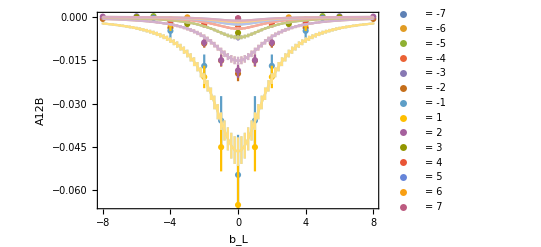

```mathematica
FitAfordiffbLbT[A12B, -1, 8, modelRefit]
```

Re A2B =>  = -1 ,eta = 8
 Fitting into   -> () = {⟨0.4647(38)⟩_(2902J), ⟨1.0826(94)⟩_(2902J), ⟨0.3980(28)⟩_(2902J)}
 chisquareDoF = 167.131

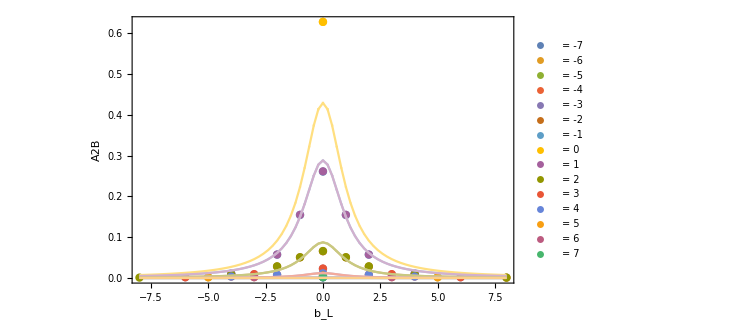

```mathematica
FitAfordiffbLbT[A2B, -1, 8, modelRefit]
```

```mathematica
FitAfordiffbLbT[A12B, -1, 8, modelRefit]
```

Re A12B =>  = -1 ,eta = 8
 Fitting into   -> () = {⟨-0.222(49)⟩_(2902J), ⟨3.29(64)⟩_(2902J), ⟨0.44(17)⟩_(2902J)}
 chisquareDoF = 1.39353

-Graphics-

Re A2B =>  = -1 ,eta = 8
 Fitting into   -> () = {⟨0.5336(57)⟩_(2902J), ⟨1.492(14)⟩_(2902J), ⟨0.5442(39)⟩_(2902J)}
 chisquareDoF = 105.296

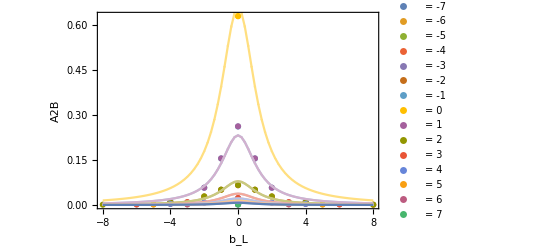

```mathematica
FitAfordiffbLbT[A2B, -1, 8, modelRefit]
```

Re A12B =>  = -2 ,eta = 8
 Fitting into   -> () = {⟨-0.120(25)⟩_(2902J), ⟨2.18(36)⟩_(2902J), ⟨-0.09 ± 0.1⟩_(2902J)}
 chisquareDoF = 2.50832

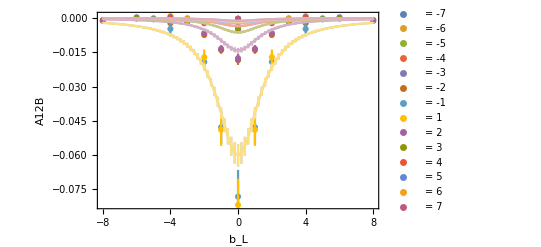

```mathematica
FitAfordiffbLbT[A12B, -2, 8, modelRefit]
```

Re A12B =>  = -3 ,eta = 8
 Fitting into   -> () = {⟨-0.061(30)⟩_(2902J), ⟨2.13(72)⟩_(2902J), ⟨-0.28(19)⟩_(2902J)}
 chisquareDoF = 0.919706

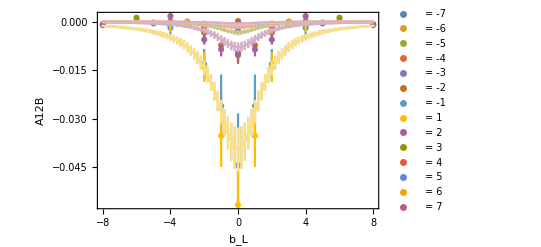

```mathematica
FitAfordiffbLbT[A12B, -3, 8, modelRefit]
```

Re A12B =>  = -4 ,eta = 8
 Fitting into   -> () =                3                                               6                                             3
{⟨-403(31) × 10 ⟩_(2902J), ⟨-3.60(20) × 10 ⟩_(2902J), ⟨-12(16) × 10 ⟩_(2902J)}
 chisquareDoF = 4.27757

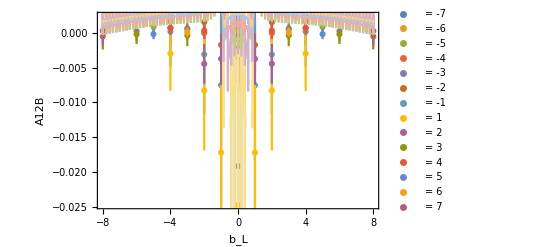

```mathematica
FitAfordiffbLbT[A12B, -4, 8, modelRefit]
```

Re A2B =>  = -2 ,eta = 8
 Fitting into   -> () = {⟨0.4506(74)⟩_(2902J), ⟨1.487(22)⟩_(2902J), ⟨0.4524(46)⟩_(2902J)}
 chisquareDoF = 44.1481

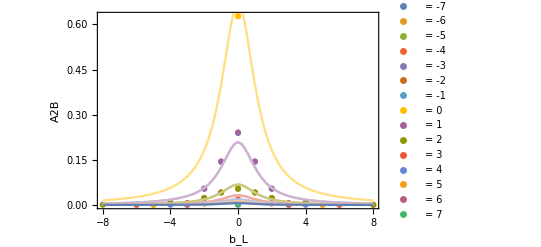

```mathematica
FitAfordiffbLbT[A2B, -2, 8, modelRefit]
```

Re A2B =>  = -3 ,eta = 8
 Fitting into   -> () = {⟨0.361(13)⟩_(2902J), ⟨1.455(39)⟩_(2902J), ⟨0.3718(71)⟩_(2902J)}
 chisquareDoF = 14.6671

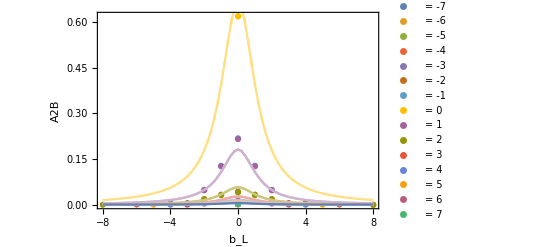

```mathematica
FitAfordiffbLbT[A2B, -3, 8, modelRefit]
```

Re A2B =>  = -4 ,eta = 8
 Fitting into   -> () = {⟨0.316(24)⟩_(2902J), ⟨1.327(74)⟩_(2902J), ⟨0.343(14)⟩_(2902J)}
 chisquareDoF = 4.04982

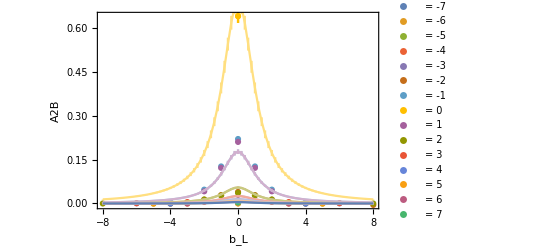

```mathematica
FitAfordiffbLbT[A2B, -4, 8, modelRefit]
```

Re A12B =>  = -1 ,eta = 8
 Fitting into   -> () = {⟨-0.0307(45)⟩_(2902J), ⟨0.121(21)⟩_(2902J), ⟨0.144(22)⟩_(2902J)}
 chisquareDoF = 1.43445

In (b.P,b^2) spcae:  Re A12B =>  = -1 ,eta = 8
 Fitting into   -> () = {⟨-0.0307(45)⟩_(2902J),⟨-0.022(25)⟩_(2902J),⟨0.144(22)⟩_(2902J)}

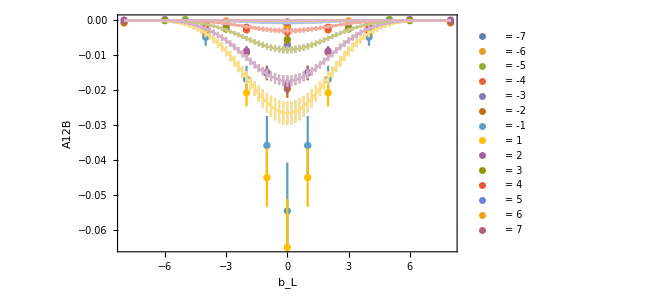

```mathematica
FitAfordiffbLbT[A12B, -1, 8, modelRefit]
```

Re A12B =>  = -2 ,eta = 8
 Fitting into   -> () = {⟨-0.069(34)⟩_(2902J), ⟨0.245(79)⟩_(2902J), ⟨0.34(14)⟩_(2902J)}
 chisquareDoF = 2.41171

In (b.P,b^2) spcae:  Re A12B =>  = -2 ,eta = 8
 Fitting into   -> () = {⟨-0.069(34)⟩_(2902J),⟨-0.024(17)⟩_(2902J),⟨0.34(14)⟩_(2902J)}

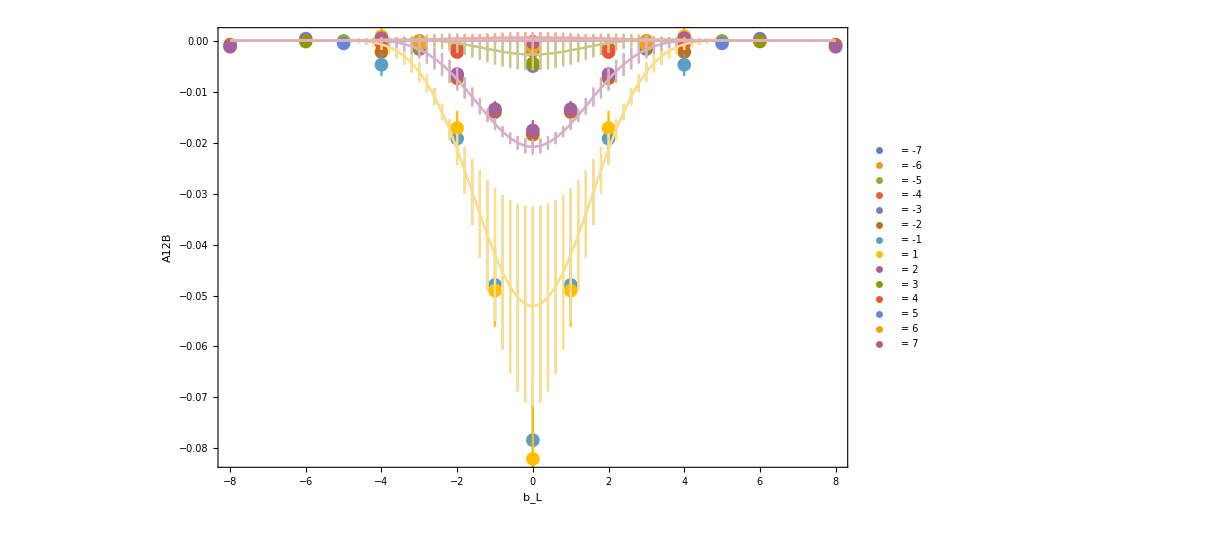

```mathematica
FitAfordiffbLbT[A12B, -2, 8, modelRefit]
```

Re A12B =>  = -3 ,eta = 8
 Fitting into   -> () = {⟨-0.058(15)⟩_(2902J), ⟨0.242(62)⟩_(2902J), ⟨0.423(82)⟩_(2902J)}
 chisquareDoF = 0.782222

In (b.P,b^2) spcae:  Re A12B =>  = -3 ,eta = 8
 Fitting into   -> () = {⟨-0.058(15)⟩_(2902J),⟨-0.0201(66)⟩_(2902J),⟨0.423(82)⟩_(2902J)}

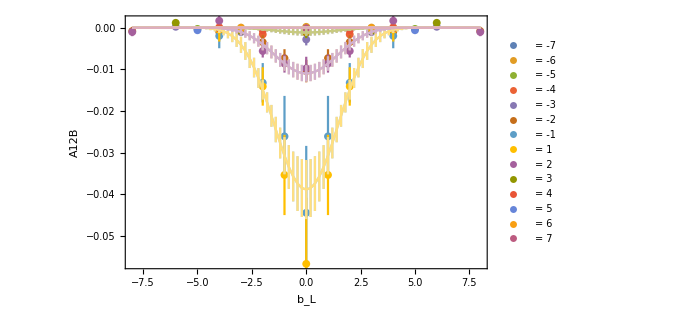

```mathematica
FitAfordiffbLbT[A12B, -3, 8, modelRefit]
```

Re A12B =>  = -4 ,eta = 8
 Fitting into   -> () = {⟨-0.031(17)⟩_(2902J), ⟨0.28(22)⟩_(2902J), ⟨0.45(26)⟩_(2902J)}
 chisquareDoF = 0.345898

In (b.P,b^2) spcae:  Re A12B =>  = -4 ,eta = 8
 Fitting into   -> () = {⟨-0.031(17)⟩_(2902J),⟨-0.010(17)⟩_(2902J),⟨0.45(26)⟩_(2902J)}

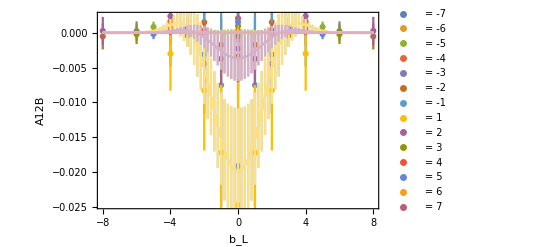

```mathematica
FitAfordiffbLbT[A12B, -4, 8, modelRefit]
```

Re A2B =>  = -1 ,eta = 8
 Fitting into   -> () = {⟨0.3724(26)⟩_(2902J), ⟨0.3612(26)⟩_(2902J), ⟨0.4039(29)⟩_(2902J)}
 chisquareDoF = 235.509

In (b.P,b^2) spcae:  Re A2B =>  = -1 ,eta = 8
 Fitting into   -> () = {⟨0.3724(26)⟩_(2902J),⟨-0.0427(27)⟩_(2902J),⟨0.4039(29)⟩_(2902J)}

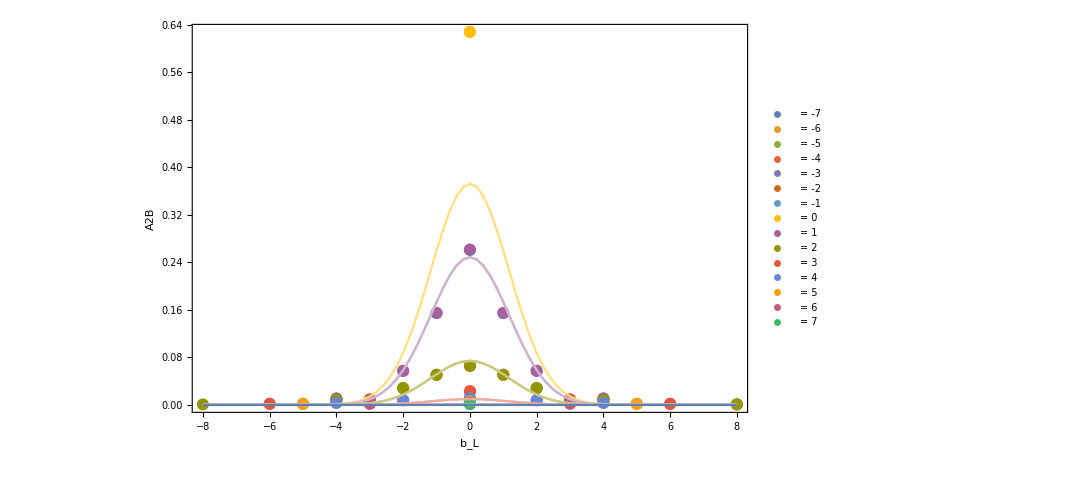

```mathematica
FitAfordiffbLbT[A2B, -1, 8, modelRefit]
```

Re A2B =>  = -2 ,eta = 8
 Fitting into   -> () = {⟨0.3693(41)⟩_(2902J), ⟨0.3650(38)⟩_(2902J), ⟨0.4594(54)⟩_(2902J)}
 chisquareDoF = 68.0216

In (b.P,b^2) spcae:  Re A2B =>  = -2 ,eta = 8
 Fitting into   -> () = {⟨0.3693(41)⟩_(2902J),⟨-0.0236(12)⟩_(2902J),⟨0.4594(54)⟩_(2902J)}

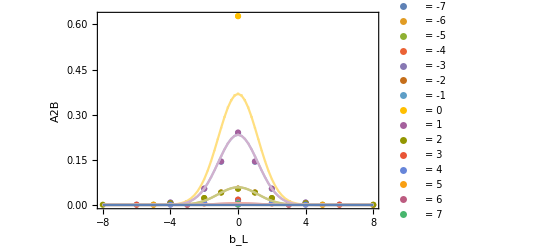

```mathematica
FitAfordiffbLbT[A2B, -2, 8, modelRefit]
```

Re A2B =>  = -3 ,eta = 8
 Fitting into   -> () = {⟨0.3568(82)⟩_(2902J), ⟨0.3787(72)⟩_(2902J), ⟨0.524(14)⟩_(2902J)}
 chisquareDoF = 14.2587

In (b.P,b^2) spcae:  Re A2B =>  = -3 ,eta = 8
 Fitting into   -> () = {⟨0.3568(82)⟩_(2902J),⟨-0.0162(13)⟩_(2902J),⟨0.524(14)⟩_(2902J)}

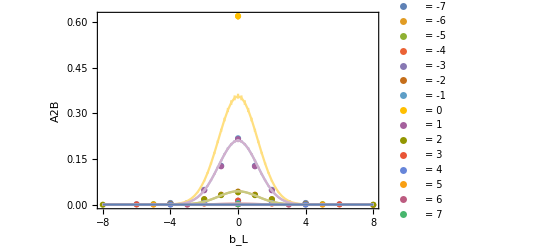

```mathematica
FitAfordiffbLbT[A2B, -3, 8, modelRefit]
```

Re A2B =>  = -4 ,eta = 8
 Fitting into   -> () = {⟨0.382(19)⟩_(2902J), ⟨0.409(17)⟩_(2902J), ⟨0.580(34)⟩_(2902J)}
 chisquareDoF = 3.22054

In (b.P,b^2) spcae:  Re A2B =>  = -4 ,eta = 8
 Fitting into   -> () = {⟨0.382(19)⟩_(2902J),⟨-0.0107(19)⟩_(2902J),⟨0.580(34)⟩_(2902J)}

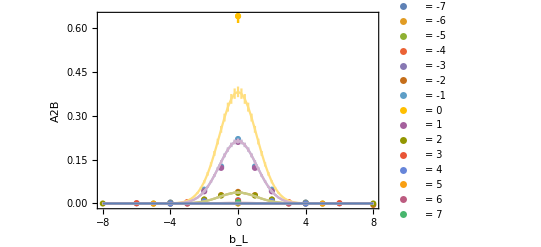

```mathematica
FitAfordiffbLbT[A2B, -4, 8, modelRefit]
```

```mathematica
modelImfit[x1_,x2_,{a_,b_,c_}]:=a*x1*(1/((x1^2)+b))*(1/((x2^2)+c));
FitImAfordiffbLbT[ampname_,P1_, etavalue_, modelfit_]:=(
dataforfit = MemDBGet[AmpDB,MemDBSelect[AmpDB,{A->ampname,PL->P1,etav->etavalue, bNum->odd}],{bL, bT,data}];
fitJK =JackknifeFit3D[dataforfit,modelfit[bL,bT,{a,b,c}],{a,b, c},{bL,bT}, modelfit];
fitParas=FitParameters/. fitJK;
fitchiDoF=chisquareDoF/. fitJK;
Print["Re ",ampname," =>  = ",P1," ,eta = ", etavalue,"\n Fitting into   -> () = ",OutputForm[fitParas],"\n chisquareDoF = ", fitchiDoF];
(*Print["In (b.P,b^2) spcae:  Re ",ampname," =>  = ",P1," ,eta = ", etavalue,"\n Fitting into   -> () = ",{OutputForm[fitParas[[1]]/P1],OutputForm[(fitParas[[2]]-fitParas[[3]])/(P1^2)],OutputForm[fitParas[[3]]] }];*)
bTlist= Union[MemDBGet[AmpDB,MemDBSelect[AmpDB,{A->ampname,PL->P1,etav->etavalue, bNum->odd}],bT]];
bLlist= Union[MemDBGet[AmpDB,MemDBSelect[AmpDB,{A->ampname,PL->P1,etav->etavalue, bNum->odd}],bL]];
PlotPLforDiffbT={};
Do[
bLAmp=MemDBGet[AmpDB,MemDBSelect[AmpDB,{A->ampname,PL->P1,etav->etavalue,bT->bTi, bNum->odd}],{bL,data}];
AppendTo[PlotPLforDiffbT,bLAmp];
 ,{bTi,bTlist}];
PlotbL= ErrorListPlot[Table[MakeErrBars[PlotPLforDiffbT[[bTi]]],{bTi, Length[bTlist]}],FrameLabel->{ , ampname}, Frame->True ,PlotRange->Full,PlotLegends->Table[" = "<>ToString[bTlist[[bTi]]],{bTi,Length[bTlist]}]];
fitbandforallbT = {};
Do[
fitbLband = {};
Do[
AppendTo[fitbLband,{bLx, modelfitJackkifband[modelfit, fitParas,bTlist[[bTx]],bLx]}];
,{bLx,Min[bLlist],Max[bLlist],0.2}];
AppendTo[fitbandforallbT,fitbLband];
,{bTx,Length[bTlist]}];
fitPlotbL=Show[PlotbL,Table[ErrorListPlot[MakeErrBars[fitbandforallbT[[bTx]]],PlotStyle->Lighter[ColorData[97,"ColorList"][[Mod[bTx,15]]],0.5],Joined->True, Frame->True],{bTx,Length[bTlist]}]];
(*fitPlotbP=Show[PlotbP,Table[Plot[modelfitJackkife[modelfit, fitParas, Pbx,bsquarelist[[bsqi]]][[1]],{Pbx,Min[Pb32by2Pilist],Max[Pb32by2Pilist]},PlotStyle->ColorData[97,"ColorList"][[Mod[bsqi,15]]]],{bsqi,Length[bsquarelist]}]];*)
Print[fitPlotbL]
)
```

Re A2B =>  = -1 ,eta = 8
 Fitting into   -> () = {⟨0.071(12)⟩_(2902J), ⟨1.18(17)⟩_(2902J), ⟨2.99(59)⟩_(2902J)}
 chisquareDoF = 1.43998

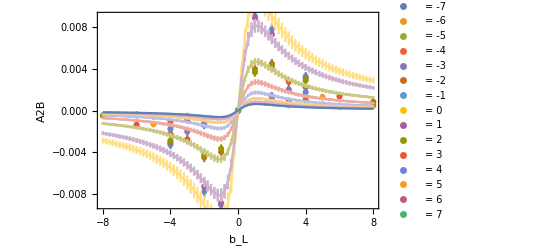

```mathematica
FitImAfordiffbLbT[A2B, -1, 8, modelImfit]
```

Re A2B =>  = -2 ,eta = 8
 Fitting into   -> () = {⟨0.077(13)⟩_(2902J), ⟨0.95(14)⟩_(2902J), ⟨1.78(36)⟩_(2902J)}
 chisquareDoF = 1.65551

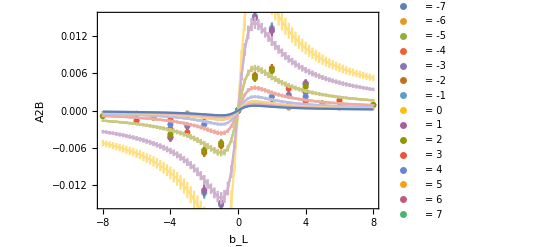

```mathematica
FitImAfordiffbLbT[A2B, -2, 8, modelImfit]
```

Re A2B =>  = -3 ,eta = 8
 Fitting into   -> () = {⟨0.042(13)⟩_(2902J), ⟨0.76(20)⟩_(2902J), ⟨0.45(31)⟩_(2902J)}
 chisquareDoF = 0.60705

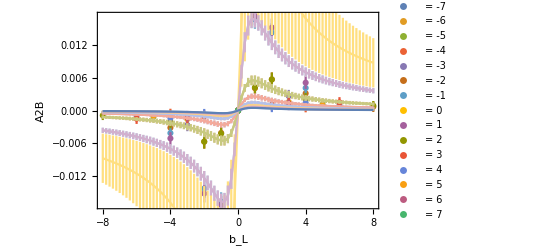

```mathematica
FitImAfordiffbLbT[A2B, -3, 8, modelImfit]
```

Re A2B =>  = -4 ,eta = 8
 Fitting into   -> () = {⟨0.026(21)⟩_(2902J), ⟨0.92(41)⟩_(2902J), ⟨-0.15(48)⟩_(2902J)}
 chisquareDoF = 0.492506

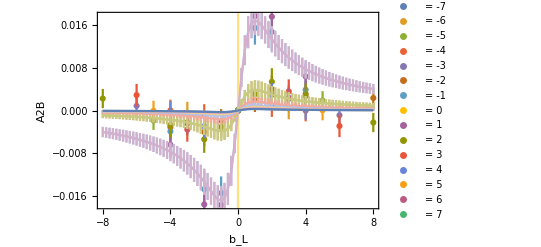

```mathematica
FitImAfordiffbLbT[A2B, -4, 8, modelImfit]
```

```mathematica
MassN = MemDBGet[AmpDBPbbsq,MemDBSelect[AmpDBPbbsq,{A->A12B,PL->-1,etav->8, bNum->even}],MN];
f[t_]:=MassN[[1]]*t/(1+t^2)*1/(1+(1+t^2))
NFourierTransform[f[t],t,1]
Table[{w,NFourierTransform[f[t],t,w]},{w,-5,5,1}]
```

0.+0.0973892 ⅈ

{{-5,0.-0.00459663 ⅈ},{-4,0.-0.0115701 ⅈ},{-3,0.-0.0276467 ⅈ},{-2,0.-0.0595045 ⅈ},{-1,0.-0.0973892 ⅈ},{0,0.},{1,0.+0.0973892 ⅈ},{2,0.+0.0595045 ⅈ},{3,0.+0.0276467 ⅈ},{4,0.+0.0115701 ⅈ},{5,0.+0.00459663 ⅈ}}

```mathematica
NFourierTransformJK[modelReA12BNfou_,pb_,x_, FourierNum_]:=Module[{numFs, modelvaluej,modelvalue, jackknifeResults},
numFs=Length[MemDBGet[AmpDBPbbsq,MemDBSelect[AmpDBPbbsq,{A->A12B,PL->-1,etav->8, bNum->even}],MN][[1]]];
modelvalue=ParallelTable[FourierNum[NFourierTransform[modelReA12BNfou[pb, j],pb,x]],{j,numFs}];
jackknifeResults=JacknifeSamples@@(modelvalue);
jackknifeResults
];
```

```mathematica
modelfitJackkifex[model_, fitParams_, x_]:=Module[{numFs, modelvaluej,modelvalue, jackknifeResults},
numFs=Length[fitParams[[1]]];
modelvaluej[j_]:=Module[{datafitParams},
datafitParams={fitParams[[1]][[j]],fitParams[[2]][[j]],fitParams[[3]][[j]]};
model[x,datafitParams]
];
modelvalue=Table[modelvaluej[j],{j,numFs}];
jackknifeResults=JacknifeSamples@@(modelvalue);
jackknifeResults
];
SiversShift[b2_,P1_, etavalue_]:=Module[{dataforfitA12B, dataforfitA2B, fitJKA12B, fitParasA12B, chisqfitA12B, fitJKA2B, fitParasA2B, chisqfitA2B, fitJKImA2B, fitParasImA2B, chisqfitImA2B},
dataforfitA12B = MemDBGet[AmpDB,MemDBSelect[AmpDB,{A->A12B,PL->P1,etav->etavalue, bNum->even}],{bL, bT,data}];
dataforfitA2B = MemDBGet[AmpDB,MemDBSelect[AmpDB,{A->A2B,PL->P1,etav->etavalue, bNum->even}],{bL, bT,data}];
dataforfitImA2BFull = MemDBGet[AmpDB,MemDBSelect[AmpDB,{A->A2B,PL->P1,etav->etavalue, bNum->odd}],{bL, bT,data}];
(*Print[" for  is removed!"];
dataforfitA2B = Select[dataforfitA2B,#[[2]]!=0&];*)
dataforfitImA2B = Select[dataforfitImA2BFull,#[[2]]!=0&];
modelfitA12B[x1_,x2_,{a_,b_,c_}]:=a*(1/((x1^2)+b))*(1/((x2^2)+c));
modelfitA2B[x1_,x2_,{a_,b_,c_}]:=a*(1/((x1^2)+b))*(1/((x2^2)+c));
modelfitImA2B[x1_,x2_,{a_,b_,c_}]:=a*x1*(1/((x1^2)+b))*(1/((x2^2)+c));
fitJKA12B =JackknifeFit3D[dataforfitA12B,modelfitA12B[bP,bsq,{a,b,c}],{a,b, c},{bP,bsq}, modelfitA12B];
fitParasA12B=FitParameters/. fitJKA12B;
chisqfitA12B=chisquareDoF/. fitJKA12B;
fitJKA2B =JackknifeFit3D[dataforfitA2B,modelfitA2B[bP,bsq,{a,b,c}],{a,b, c},{bP,bsq}, modelfitA2B];
fitParasA2B=FitParameters/. fitJKA2B;
chisqfitA2B=chisquareDoF/. fitJKA2B;
fitJKImA2B =JackknifeFit3D[dataforfitImA2B,modelfitImA2B[bP,bsq,{a,b,c}],{a,b, c},{bP,bsq}, modelfitImA2B];
fitParasImA2B=FitParameters/. fitJKImA2B;
chisqfitImA2B=chisquareDoF/. fitJKImA2B;
Print["Fitting:    -> () = ",OutputForm[fitParasA12B], ", chisquareDoF = ", chisqfitA12B,"\n Fitting:    -> () = ",OutputForm[fitParasA2B], ", chisquareDoF = ", chisqfitA2B, "\n Fitting:   -> () = ",OutputForm[fitParasImA2B]," chisquareDoF = ", chisqfitImA2B, "\n  = ",b2, "  = ",P1," ,eta = ", etavalue];
b2II = b2*fitParasA12B[[1]]/fitParasA12B[[1]];
II= fitParasA12B[[1]]/fitParasA12B[[1]];
fitaA12B =fitParasA12B[[1]];
fitbA12B=fitParasA12B[[2]];
fitcA12B =fitParasA12B[[3]];
fitaA2B =fitParasA2B[[1]];
fitbA2B=fitParasA2B[[2]];
fitcA2B =fitParasA2B[[3]];
fitaImA2B =fitParasImA2B[[1]];
fitbImA2B=fitParasImA2B[[2]];
fitcImA2B =fitParasImA2B[[3]];
MassN = MemDBGet[AmpDBPbbsq,MemDBSelect[AmpDBPbbsq,{A->A12B,PL->P1,etav->etavalue, bNum->even}],MN][[1]];
(*reducedratioA12B=(fitaA12B/(fitcA12B+b2II))*(II/(2*fitbA12B));
fourierA12B[x_, {reducedr_, bA12B_, cA12B_}] :=Sech[((N[Pi]*x)/(2*bA12B))]*reducedr;
reducedratioA2B=(fitaA2B/(fitcA2B+b2II))*(II/(2*fitbA2B));
reducedratioImA2B=(fitaImA2B/(fitcImA2B+b2II))*(II/(2*Sqrt[2]*(fitbImA2B)^(3/2)));
fourierA2B[x_, {reducedr_, bA2B_, bImA2B_}] :=Sech[((N[Pi]*x)/(2*bA2B))]*reducedr;
(*Print[reducedratioImA2B];*)
fourierImA2B[x_, {reducedr_, bA2B_, cA2B_}] :=x*Exp[-(x^2)/(4*bA2B)]*reducedr;
(*reducedratio1 = -MassN*(197*0.0001/lata)*reducedratioA12B/reducedratioA2B;
siversratio[x_, {reducedr1_, bA12B_, bA2B_}] := reducedr1*(Sech[((N[Pi]*x)/(2*bA12B))]/Sech[((N[Pi]*x)/(2*bA2B))]);*)*)
massterm=-MassN[[1]]*(197*0.0001/lata);
siversshiftxforplot={};
fourieA12Bxforplot={};
fourieA2Bxforplot={};
Do[
(*siversrforx = modelfitJackkifex[siversratio,{reducedratio1, fitbA12B, fitbA2B}, x];*)
modelReA12BNfou[pb_, jknum_]:=fitaA12B[[jknum]]*1/(fitbA12B[[jknum]]+((pb^2)/(P1^2)))*1/(fitcA12B[[jknum]]+(b2^2+((pb^2)/(P1^2))));
modelReA2BNfou[pb_, jknum_]:=fitaA2B[[jknum]]*1/(fitbA2B[[jknum]]+((pb^2)/(P1^2)))*1/(fitcA2B[[jknum]]+(b2^2+((pb^2)/(P1^2))));
modelImA2BNfou[pb_, jknum_]:=fitaImA2B[[jknum]]*((pb)/(-P1))*1/(fitbImA2B[[jknum]]+((pb^2)/(P1^2)))*1/(fitcImA2B[[jknum]]+(b2^2+((pb^2)/(P1^2))));
fourierA12Bforx = NFourierTransformJK[modelReA12BNfou,pb,x, Re];
fourierREA2Bforx=NFourierTransformJK[modelReA2BNfou,pb,x, Re];
fourierIMA2Bforx=NFourierTransformJK[modelImA2BNfou,pb,x, Im];
fourierA2Bforx=fourierREA2Bforx-fourierIMA2Bforx;
siversrforx=massterm*fourierA12Bforx/fourierA2Bforx;
AppendTo[siversshiftxforplot,{x,siversrforx}];
AppendTo[fourieA12Bxforplot,{x,fourierA12Bforx}];
AppendTo[fourieA2Bxforplot,{x,fourierA2Bforx}];
,{x,0,1, 0.01}];
MkErrA12B=MakeErrBars[fourieA12Bxforplot];
A12BPltrangMin=(MkErrA12B[[1]][[1]][[2]]+MkErrA12B[[1]][[2]][[1]][[1]])*0.5;
A12BPltrangMax=(MkErrA12B[[1]][[1]][[2]]+MkErrA12B[[1]][[2]][[1]][[2]])*1.5;
PlotfourieA12Bx = ErrorListPlot[MkErrA12B,FrameLabel->{ , }, Frame->True , PlotRange->{{Automatic,Automatic},{0,A12BPltrangMax}}];(* {{Automatic,Automatic},{0,0.0004}}*)
Print[PlotfourieA12Bx];
MkErrA2B=MakeErrBars[fourieA2Bxforplot];
A2BPltrangMin=(MkErrA2B[[1]][[1]][[2]]+MkErrA2B[[1]][[2]][[1]][[1]])*0.5;
A2BPltrangMax=(MkErrA2B[[1]][[1]][[2]]+MkErrA2B[[1]][[2]][[1]][[2]])*2;
PlotfourieA2Bx= ErrorListPlot[MkErrA2B,FrameLabel->{ , }, Frame->True , PlotRange->Full];(*{{Automatic,Automatic},{0.0045,0.0055}}*)
Print[PlotfourieA2Bx];
Print["Sivers shift in GeV"];
MkErrsiversshift=MakeErrBars[siversshiftxforplot];
SsPltrangMin=(MkErrsiversshift[[1]][[1]][[2]]-MkErrsiversshift[[1]][[2]][[1]][[1]])*0.5;
SsPltrangMax=(MkErrsiversshift[[1]][[1]][[2]]-MkErrsiversshift[[1]][[2]][[1]][[2]])*1.2;
Plotsivershift = ErrorListPlot[MkErrsiversshift,FrameLabel->{ , }, Frame->True , PlotRange->{{Automatic,Automatic},{0,0.04}}];(* PlotRange->{{Automatic,Automatic},{-0.3,0}}*)
Print[Plotsivershift];
(*Export["/Users/hariprashadravikumar/Downloads/Lorentz_bL_Lorentz_bT_Fourierx_A12B_"<>ToString[ampname]<>"_b_"<>ToString[bnum]<>"_P1_"<>ToString[P1]<>"_eta_"<>ToString[etavalue]<>".pdf",PlotfourieA12Bx,"PDF",ImageResolution->600];
Export["/Users/hariprashadravikumar/Downloads/Lorentz_bL_Lorentz_bT_Fourierx_A2B_"<>ToString[ampname]<>"_b_"<>ToString[bnum]<>"_P1_"<>ToString[P1]<>"_eta_"<>ToString[etavalue]<>".pdf",PlotfourieA2Bx,"PDF",ImageResolution->600];
Export["/Users/hariprashadravikumar/Downloads/Lorentz_bL_Lorentz_bT_Fourierx_SiversShift_"<>ToString[ampname]<>"_b_"<>ToString[bnum]<>"_P1_"<>ToString[P1]<>"_eta_"<>ToString[etavalue]<>".pdf",Plotsivershift,"PDF",ImageResolution->600];*)
];
```

Fitting:    -> () = {⟨-0.222(49)⟩_(2902J), ⟨3.29(64)⟩_(2902J), ⟨0.44(17)⟩_(2902J)}, chisquareDoF = 1.39353
 Fitting:    -> () = {⟨0.5336(57)⟩_(2902J), ⟨1.492(14)⟩_(2902J), ⟨0.5442(39)⟩_(2902J)}, chisquareDoF = 105.296
 Fitting:   -> () = {⟨0.071(12)⟩_(2902J), ⟨1.18(17)⟩_(2902J), ⟨2.99(59)⟩_(2902J)} chisquareDoF = 1.46321
  = 9  = -1 ,eta = 8

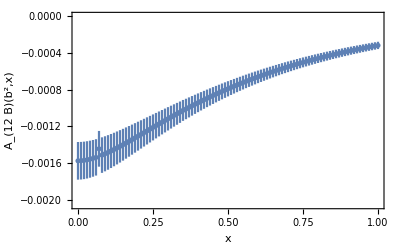

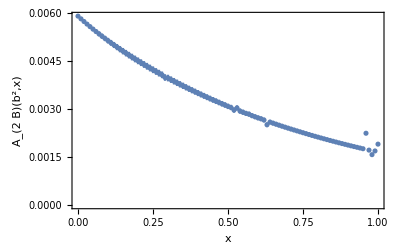

Sivers shift in GeV

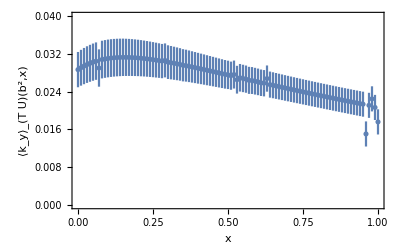

```mathematica
SiversShift[9,-1, 8]
```

Fitting:    -> () = {⟨-0.120(25)⟩_(2902J), ⟨2.18(36)⟩_(2902J), ⟨-0.09 ± 0.1⟩_(2902J)}, chisquareDoF = 2.50832
 Fitting:    -> () = {⟨0.4506(74)⟩_(2902J), ⟨1.487(22)⟩_(2902J), ⟨0.4524(46)⟩_(2902J)}, chisquareDoF = 44.1481
 Fitting:   -> () = {⟨0.077(13)⟩_(2902J), ⟨0.95(14)⟩_(2902J), ⟨1.78(36)⟩_(2902J)} chisquareDoF = 1.68221
  = 9  = -2 ,eta = 8

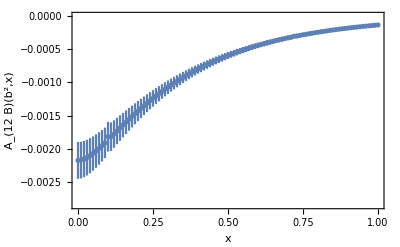

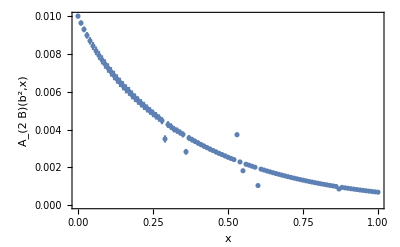

Sivers shift in GeV

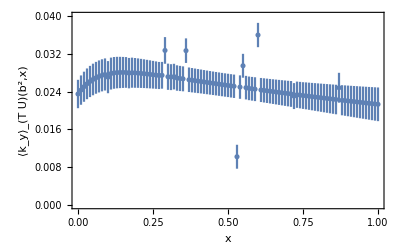

```mathematica
SiversShift[9,-2, 8]
```

Fitting:    -> () = {⟨-0.061(30)⟩_(2902J), ⟨2.13(72)⟩_(2902J), ⟨-0.28(19)⟩_(2902J)}, chisquareDoF = 0.919706
 Fitting:    -> () = {⟨0.361(13)⟩_(2902J), ⟨1.455(39)⟩_(2902J), ⟨0.3718(71)⟩_(2902J)}, chisquareDoF = 14.6671
 Fitting:   -> () = {⟨0.042(13)⟩_(2902J), ⟨0.76(20)⟩_(2902J), ⟨0.45(31)⟩_(2902J)} chisquareDoF = 0.616842
  = 9  = -3 ,eta = 8

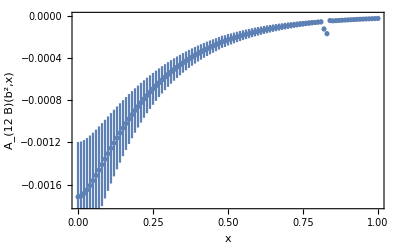

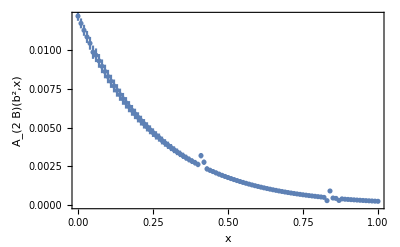

Sivers shift in GeV

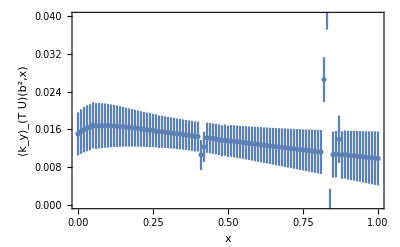

```mathematica
SiversShift[9,-3, 8]
```

Fitting:    -> () =                3                                               6                                             3
{⟨-403(31) × 10 ⟩_(2902J), ⟨-3.60(20) × 10 ⟩_(2902J), ⟨-12(16) × 10 ⟩_(2902J)}, chisquareDoF = 4.27757
 Fitting:    -> () = {⟨0.316(24)⟩_(2902J), ⟨1.327(74)⟩_(2902J), ⟨0.343(14)⟩_(2902J)}, chisquareDoF = 4.04982
 Fitting:   -> () = {⟨0.026(21)⟩_(2902J), ⟨0.92(41)⟩_(2902J), ⟨-0.15(48)⟩_(2902J)} chisquareDoF = 0.500449
  = 9  = -4 ,eta = 8

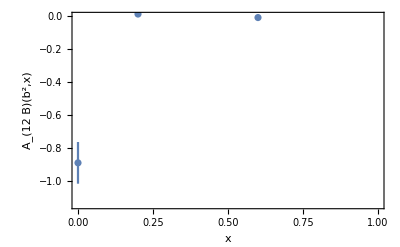

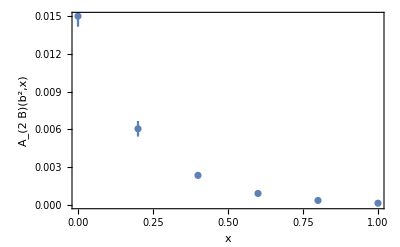

Sivers shift in GeV

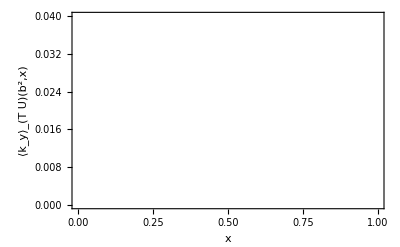

```mathematica
SiversShift[9,-4, 8]
```

```mathematica
SiversShift2[b2_,P1_, etavalue_]:=Module[{dataforfitA12B, dataforfitA2B, fitJKA12B, fitParasA12B, chisqfitA12B, fitJKA2B, fitParasA2B, chisqfitA2B, fitJKImA2B, fitParasImA2B, chisqfitImA2B},
dataforfitA12B = MemDBGet[AmpDB,MemDBSelect[AmpDB,{A->A12B,PL->P1,etav->etavalue, bNum->even}],{bL, bT,data}];
dataforfitA2B = MemDBGet[AmpDB,MemDBSelect[AmpDB,{A->A2B,PL->P1,etav->etavalue, bNum->even}],{bL, bT,data}];
dataforfitImA2BFull = MemDBGet[AmpDB,MemDBSelect[AmpDB,{A->A2B,PL->P1,etav->etavalue, bNum->odd}],{bL, bT,data}];
(*Print[" for  is removed!"];
dataforfitA2B = Select[dataforfitA2B,#[[2]]!=0&];*)
dataforfitImA2B = Select[dataforfitImA2BFull,#[[2]]!=0&];
modelfitA12B[x1_,x2_,{a_,b_,c_}]:=a*Exp[(-b*x1^2)]*(1/((x2^2)+c));
modelfitA2B[x1_,x2_,{a_,b_,c_}]:=a*Exp[(-b*x1^2)]*(1/((x2^2)+c));
modelfitImA2B[x1_,x2_,{a_,b_,c_}]:=a*x1*Exp[(-b*x1^2)]*(1/((x2^2)+c));
fitJKA12B =JackknifeFit3D[dataforfitA12B,modelfitA12B[bP,bsq,{a,b,c}],{a,b, c},{bP,bsq}, modelfitA12B];
fitParasA12B=FitParameters/. fitJKA12B;
chisqfitA12B=chisquareDoF/. fitJKA12B;
fitJKA2B =JackknifeFit3D[dataforfitA2B,modelfitA2B[bP,bsq,{a,b,c}],{a,b, c},{bP,bsq}, modelfitA2B];
fitParasA2B=FitParameters/. fitJKA2B;
chisqfitA2B=chisquareDoF/. fitJKA2B;
fitJKImA2B =JackknifeFit3D[dataforfitImA2B,modelfitImA2B[bP,bsq,{a,b,c}],{a,b, c},{bP,bsq}, modelfitImA2B];
fitParasImA2B=FitParameters/. fitJKImA2B;
chisqfitImA2B=chisquareDoF/. fitJKImA2B;
Print["Fitting:    -> () = ",OutputForm[fitParasA12B], ", chisquareDoF = ", chisqfitA12B,"\n Fitting:    -> () = ",OutputForm[fitParasA2B], ", chisquareDoF = ", chisqfitA2B, "\n Fitting:   -> () = ",OutputForm[fitParasImA2B]," chisquareDoF = ", chisqfitImA2B, "\n  = ",b2, "  = ",P1," ,eta = ", etavalue];
b2II = b2*fitParasA12B[[1]]/fitParasA12B[[1]];
II= fitParasA12B[[1]]/fitParasA12B[[1]];
fitaA12B =fitParasA12B[[1]];
fitbA12B=fitParasA12B[[2]];
fitcA12B =fitParasA12B[[3]];
fitaA2B =fitParasA2B[[1]];
fitbA2B=fitParasA2B[[2]];
fitcA2B =fitParasA2B[[3]];
fitaImA2B =fitParasImA2B[[1]];
fitbImA2B=fitParasImA2B[[2]];
fitcImA2B =fitParasImA2B[[3]];
MassN = MemDBGet[AmpDBPbbsq,MemDBSelect[AmpDBPbbsq,{A->A12B,PL->P1,etav->etavalue, bNum->even}],MN][[1]];
massterm=-MassN[[1]]*(197*0.0001/lata);
siversshiftxforplot={};
fourieA12Bxforplot={};
fourieA2Bxforplot={};
Do[
(*siversrforx = modelfitJackkifex[siversratio,{reducedratio1, fitbA12B, fitbA2B}, x];*)
modelReA12BNfou[pb_, jknum_]:=fitaA12B[[jknum]]*Exp[(-fitbA12B[[jknum]]*((pb^2)/(P1^2)))]*1/(fitcA12B[[jknum]]+(b2^2+((pb^2)/(P1^2))));
modelReA2BNfou[pb_, jknum_]:=fitaA2B[[jknum]]*Exp[(-fitbA2B[[jknum]]*((pb^2)/(P1^2)))]*1/(fitcA2B[[jknum]]+(b2^2+((pb^2)/(P1^2))));
modelImA2BNfou[pb_, jknum_]:=fitaImA2B[[jknum]]*((pb)/(-P1))*Exp[(-fitbImA2B[[jknum]]*((pb^2)/(P1^2)))]*1/(fitcImA2B[[jknum]]+(b2^2+((pb^2)/(P1^2))));
fourierA12Bforx = NFourierTransformJK[modelReA12BNfou,pb,x, Re];
fourierREA2Bforx=NFourierTransformJK[modelReA2BNfou,pb,x, Re];
fourierIMA2Bforx=NFourierTransformJK[modelImA2BNfou,pb,x, Im];
fourierA2Bforx=fourierREA2Bforx-fourierIMA2Bforx;
siversrforx=massterm*fourierA12Bforx/fourierA2Bforx;
AppendTo[siversshiftxforplot,{x,siversrforx}];
AppendTo[fourieA12Bxforplot,{x,fourierA12Bforx}];
AppendTo[fourieA2Bxforplot,{x,fourierA2Bforx}];
,{x,0,1, 0.2}];
MkErrA12B=MakeErrBars[fourieA12Bxforplot];
A12BPltrangMin=(MkErrA12B[[1]][[1]][[2]]+MkErrA12B[[1]][[2]][[1]][[1]])*0.5;
A12BPltrangMax=(MkErrA12B[[1]][[1]][[2]]+MkErrA12B[[1]][[2]][[1]][[2]])*1.2;
PlotfourieA12Bx = ErrorListPlot[MkErrA12B,FrameLabel->{ , }, Frame->True , PlotRange->{{Automatic,Automatic},{0,A12BPltrangMax}}];(* {{Automatic,Automatic},{0,0.0004}}*)
Print[PlotfourieA12Bx];
MkErrA2B=MakeErrBars[fourieA2Bxforplot];
A2BPltrangMin=(MkErrA2B[[1]][[1]][[2]]+MkErrA2B[[1]][[2]][[1]][[1]])*0.5;
A2BPltrangMax=(MkErrA2B[[1]][[1]][[2]]+MkErrA2B[[1]][[2]][[1]][[2]])*2;
PlotfourieA2Bx= ErrorListPlot[MkErrA2B,FrameLabel->{ , }, Frame->True , PlotRange->Full];(*{{Automatic,Automatic},{0.0045,0.0055}}*)
Print[PlotfourieA2Bx];
Print["Sivers shift in GeV"];
MkErrsiversshift=MakeErrBars[siversshiftxforplot];
SsPltrangMin=(MkErrsiversshift[[1]][[1]][[2]]-MkErrsiversshift[[1]][[2]][[1]][[1]])*0.5;
SsPltrangMax=(MkErrsiversshift[[1]][[1]][[2]]-MkErrsiversshift[[1]][[2]][[1]][[2]])*1.2;
Plotsivershift = ErrorListPlot[MkErrsiversshift,FrameLabel->{ , }, Frame->True , PlotRange->{{Automatic,Automatic},{0,0.04}}];(* PlotRange->{{Automatic,Automatic},{-0.3,0}}*)
Print[Plotsivershift];
Export["/Users/hariprashadravikumar/Downloads/Gaussian_bL_Lorentz_bT_Fourierx_A12B_"<>ToString[ampname]<>"_b_"<>ToString[bnum]<>"_P1_"<>ToString[P1]<>"_eta_"<>ToString[etavalue]<>".pdf",PlotfourieA12Bx,"PDF",ImageResolution->600];
Export["/Users/hariprashadravikumar/Downloads/Gaussian_bL_Lorentz_bT_Fourierx_A2B_"<>ToString[ampname]<>"_b_"<>ToString[bnum]<>"_P1_"<>ToString[P1]<>"_eta_"<>ToString[etavalue]<>".pdf",PlotfourieA2Bx,"PDF",ImageResolution->600];
Export["/Users/hariprashadravikumar/Downloads/Gaussian_bL_Lorentz_bT_Fourierx_SiversShift_"<>ToString[ampname]<>"_b_"<>ToString[bnum]<>"_P1_"<>ToString[P1]<>"_eta_"<>ToString[etavalue]<>".pdf",Plotsivershift,"PDF",ImageResolution->600];
];
```

Fitting:    -> () = {⟨-0.0639(69)⟩_(2902J), ⟨0.128(22)⟩_(2902J), ⟨0.56(18)⟩_(2902J)}, chisquareDoF = 1.11606
 Fitting:    -> () = {⟨0.3115(25)⟩_(2902J), ⟨0.2966(24)⟩_(2902J), ⟨0.4857(33)⟩_(2902J)}, chisquareDoF = 127.98
 Fitting:   -> () = {⟨0.0287(35)⟩_(2902J), ⟨0.1327(89)⟩_(2902J), ⟨2.85(50)⟩_(2902J)} chisquareDoF = 2.31827
  = 9  = -1 ,eta = 8

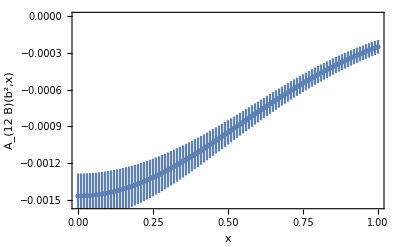

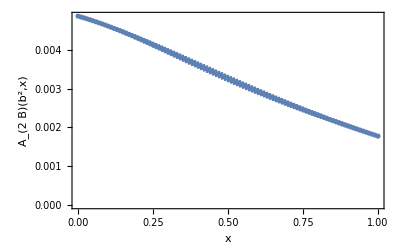

Sivers shift in GeV

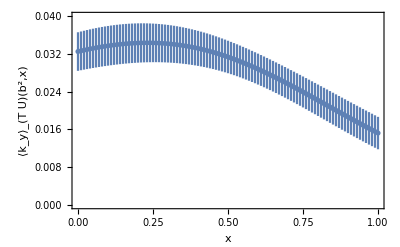

```mathematica
SiversShift2[9,-1, 8]
```

Fitting:    -> () = {⟨-0.0531(49)⟩_(2902J), ⟨0.195(30)⟩_(2902J), ⟨-0.02 ± 0.11⟩_(2902J)}, chisquareDoF = 1.96869
 Fitting:    -> () = {⟨0.2663(32)⟩_(2902J), ⟨0.2942(37)⟩_(2902J), ⟨0.4061(40)⟩_(2902J)}, chisquareDoF = 35.8242
 Fitting:   -> () = {⟨0.0370(43)⟩_(2902J), ⟨0.153(11)⟩_(2902J), ⟨1.66(33)⟩_(2902J)} chisquareDoF = 2.02277
  = 9  = -2 ,eta = 8

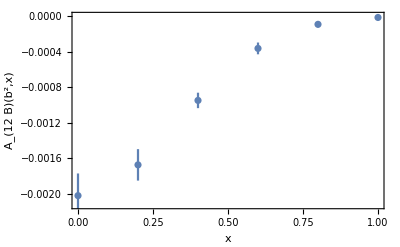

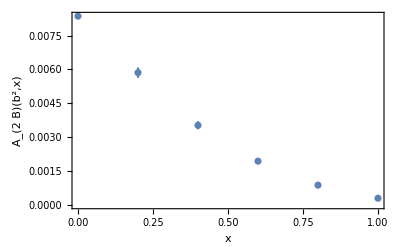

Sivers shift in GeV

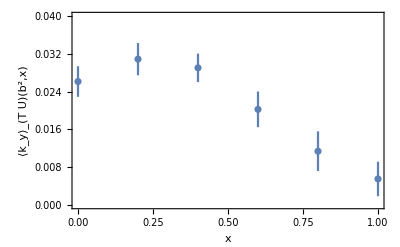

```mathematica
SiversShift2[9,-2, 8]
```

Fitting:    -> () = {⟨-0.0286(64)⟩_(2902J), ⟨0.189(49)⟩_(2902J), ⟨-0.21(19)⟩_(2902J)}, chisquareDoF = 0.730716
 Fitting:    -> () = {⟨0.2194(49)⟩_(2902J), ⟨0.2980(66)⟩_(2902J), ⟨0.3342(60)⟩_(2902J)}, chisquareDoF = 9.03983
 Fitting:   -> () = {⟨0.0241(56)⟩_(2902J), ⟨0.169(19)⟩_(2902J), ⟨0.43(30)⟩_(2902J)} chisquareDoF = 0.633471
  = 9  = -3 ,eta = 8

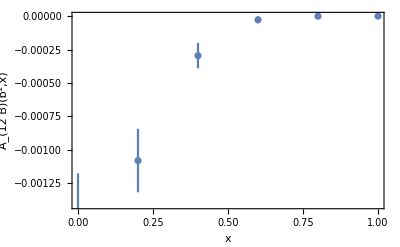

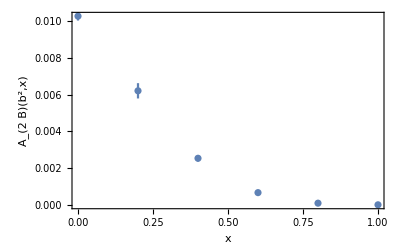

Sivers shift in GeV

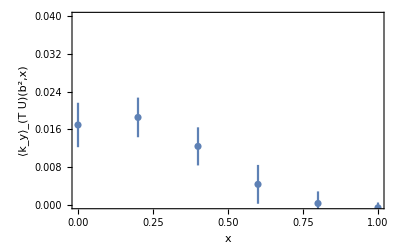

```mathematica
SiversShift2[9,-3, 8]
```

```mathematica
SiversShift3[b2_,P1_, etavalue_]:=Module[{dataforfitA12B, dataforfitA2B, fitJKA12B, fitParasA12B, chisqfitA12B, fitJKA2B, fitParasA2B, chisqfitA2B, fitJKImA2B, fitParasImA2B, chisqfitImA2B},
dataforfitA12B = MemDBGet[AmpDB,MemDBSelect[AmpDB,{A->A12B,PL->P1,etav->etavalue, bNum->even}],{bL, bT,data}];
dataforfitA2B = MemDBGet[AmpDB,MemDBSelect[AmpDB,{A->A2B,PL->P1,etav->etavalue, bNum->even}],{bL, bT,data}];
dataforfitImA2BFull = MemDBGet[AmpDB,MemDBSelect[AmpDB,{A->A2B,PL->P1,etav->etavalue, bNum->odd}],{bL, bT,data}];
(*Print[" for  is removed!"];
dataforfitA2B = Select[dataforfitA2B,#[[2]]!=0&];*)
dataforfitImA2B = Select[dataforfitImA2BFull,#[[2]]!=0&];
modelfitA12B[x1_,x2_,{a_,b_,c_}]:=a*(1/((x1^2)+b))*Exp[(-c*x2^2)];
modelfitA2B[x1_,x2_,{a_,b_,c_}]:=a*(1/((x1^2)+b))*Exp[(-c*x2^2)];
modelfitImA2B[x1_,x2_,{a_,b_,c_}]:=a*x1*(1/((x1^2)+b))*Exp[(-c*x2^2)];
fitJKA12B =JackknifeFit3D[dataforfitA12B,modelfitA12B[bP,bsq,{a,b,c}],{a,b, c},{bP,bsq}, modelfitA12B];
fitParasA12B=FitParameters/. fitJKA12B;
chisqfitA12B=chisquareDoF/. fitJKA12B;
fitJKA2B =JackknifeFit3D[dataforfitA2B,modelfitA2B[bP,bsq,{a,b,c}],{a,b, c},{bP,bsq}, modelfitA2B];
fitParasA2B=FitParameters/. fitJKA2B;
chisqfitA2B=chisquareDoF/. fitJKA2B;
fitJKImA2B =JackknifeFit3D[dataforfitImA2B,modelfitImA2B[bP,bsq,{a,b,c}],{a,b, c},{bP,bsq}, modelfitImA2B];
fitParasImA2B=FitParameters/. fitJKImA2B;
chisqfitImA2B=chisquareDoF/. fitJKImA2B;
Print["Fitting:    -> () = ",OutputForm[fitParasA12B], ", chisquareDoF = ", chisqfitA12B,"\n Fitting:    -> () = ",OutputForm[fitParasA2B], ", chisquareDoF = ", chisqfitA2B, "\n Fitting:   -> () = ",OutputForm[fitParasImA2B]," chisquareDoF = ", chisqfitImA2B, "\n  = ",b2, "  = ",P1," ,eta = ", etavalue];
b2II = b2*fitParasA12B[[1]]/fitParasA12B[[1]];
II= fitParasA12B[[1]]/fitParasA12B[[1]];
fitaA12B =fitParasA12B[[1]];
fitbA12B=fitParasA12B[[2]];
fitcA12B =fitParasA12B[[3]];
fitaA2B =fitParasA2B[[1]];
fitbA2B=fitParasA2B[[2]];
fitcA2B =fitParasA2B[[3]];
fitaImA2B =fitParasImA2B[[1]];
fitbImA2B=fitParasImA2B[[2]];
fitcImA2B =fitParasImA2B[[3]];
MassN = MemDBGet[AmpDBPbbsq,MemDBSelect[AmpDBPbbsq,{A->A12B,PL->P1,etav->etavalue, bNum->even}],MN][[1]];
massterm=-MassN[[1]]*(197*0.0001/lata);
siversshiftxforplot={};
fourieA12Bxforplot={};
fourieA2Bxforplot={};
Do[
(*siversrforx = modelfitJackkifex[siversratio,{reducedratio1, fitbA12B, fitbA2B}, x];*)
modelReA12BNfou[pb_, jknum_]:=fitaA12B[[jknum]]*Exp[(-fitbA12B[[jknum]]*((pb^2)/(P1^2)))]*1/(fitcA12B[[jknum]]+(b2^2+((pb^2)/(P1^2))));
modelReA2BNfou[pb_, jknum_]:=fitaA2B[[jknum]]*Exp[(-fitbA2B[[jknum]]*((pb^2)/(P1^2)))]*1/(fitcA2B[[jknum]]+(b2^2+((pb^2)/(P1^2))));
modelImA2BNfou[pb_, jknum_]:=fitaImA2B[[jknum]]*((pb)/(-P1))*Exp[(-fitbImA2B[[jknum]]*((pb^2)/(P1^2)))]*1/(fitcImA2B[[jknum]]+(b2^2+((pb^2)/(P1^2))));
fourierA12Bforx = NFourierTransformJK[modelReA12BNfou,pb,x, Re];
fourierREA2Bforx=NFourierTransformJK[modelReA2BNfou,pb,x, Re];
fourierIMA2Bforx=NFourierTransformJK[modelImA2BNfou,pb,x, Im];
fourierA2Bforx=fourierREA2Bforx-fourierIMA2Bforx;
siversrforx=massterm*fourierA12Bforx/fourierA2Bforx;
AppendTo[siversshiftxforplot,{x,siversrforx}];
AppendTo[fourieA12Bxforplot,{x,fourierA12Bforx}];
AppendTo[fourieA2Bxforplot,{x,fourierA2Bforx}];
,{x,0,1, 0.01}];
MkErrA12B=MakeErrBars[fourieA12Bxforplot];
A12BPltrangMin=(MkErrA12B[[1]][[1]][[2]]+MkErrA12B[[1]][[2]][[1]][[1]])*0.5;
A12BPltrangMax=(MkErrA12B[[1]][[1]][[2]]+MkErrA12B[[1]][[2]][[1]][[2]])*1.2;
PlotfourieA12Bx = ErrorListPlot[MkErrA12B,FrameLabel->{ , }, Frame->True , PlotRange->Full];(* {{Automatic,Automatic},{0,0.0004}}*)
Print[PlotfourieA12Bx];
MkErrA2B=MakeErrBars[fourieA2Bxforplot];
A2BPltrangMin=(MkErrA2B[[1]][[1]][[2]]+MkErrA2B[[1]][[2]][[1]][[1]])*0.5;
A2BPltrangMax=(MkErrA2B[[1]][[1]][[2]]+MkErrA2B[[1]][[2]][[1]][[2]])*2;
PlotfourieA2Bx= ErrorListPlot[MkErrA2B,FrameLabel->{ , }, Frame->True , PlotRange->Full];(*{{Automatic,Automatic},{0.0045,0.0055}}*)
Print[PlotfourieA2Bx];
Print["Sivers shift in GeV"];
MkErrsiversshift=MakeErrBars[siversshiftxforplot];
SsPltrangMin=(MkErrsiversshift[[1]][[1]][[2]]-MkErrsiversshift[[1]][[2]][[1]][[1]])*0.5;
SsPltrangMax=(MkErrsiversshift[[1]][[1]][[2]]-MkErrsiversshift[[1]][[2]][[1]][[2]])*1.2;
Plotsivershift = ErrorListPlot[MkErrsiversshift,FrameLabel->{ , }, Frame->True , PlotRange->{{Automatic,Automatic},{0,0.04}}];(* PlotRange->{{Automatic,Automatic},{-0.3,0}}*)
Print[Plotsivershift];
Export["/Users/hariprashadravikumar/Downloads/Lorentz_bL_Gaussian_bT_Fourierx_A12B_"<>ToString[ampname]<>"_b_"<>ToString[bnum]<>"_P1_"<>ToString[P1]<>"_eta_"<>ToString[etavalue]<>".pdf",PlotfourieA12Bx,"PDF",ImageResolution->600];
Export["/Users/hariprashadravikumar/Downloads/Lorentz_bL_Gaussian_bT_Fourierx_A2B_"<>ToString[ampname]<>"_b_"<>ToString[bnum]<>"_P1_"<>ToString[P1]<>"_eta_"<>ToString[etavalue]<>".pdf",PlotfourieA2Bx,"PDF",ImageResolution->600];
Export["/Users/hariprashadravikumar/Downloads/Lorentz_bL_Gaussian_bT_Fourierx_SiversShift_"<>ToString[ampname]<>"_b_"<>ToString[bnum]<>"_P1_"<>ToString[P1]<>"_eta_"<>ToString[etavalue]<>".pdf",Plotsivershift,"PDF",ImageResolution->600];
];
```

Fitting:    -> () = {⟨-0.125(20)⟩_(2902J), ⟨3.44(69)⟩_(2902J), ⟨0.153(28)⟩_(2902J)}, chisquareDoF = 1.6132
 Fitting:    -> () = {⟨0.4647(38)⟩_(2902J), ⟨1.0826(94)⟩_(2902J), ⟨0.3980(28)⟩_(2902J)}, chisquareDoF = 167.131
 Fitting:   -> () = {⟨0.0180(19)⟩_(2902J), ⟨1.29(17)⟩_(2902J), ⟨0.108(23)⟩_(2902J)} chisquareDoF = 2.25728
  = 9  = -1 ,eta = 8

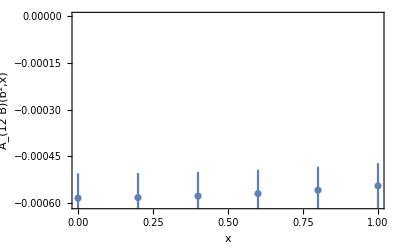

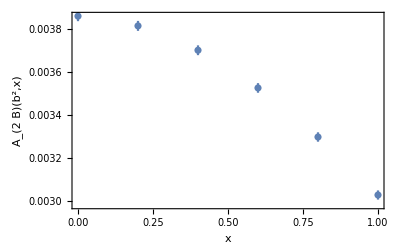

Sivers shift in GeV

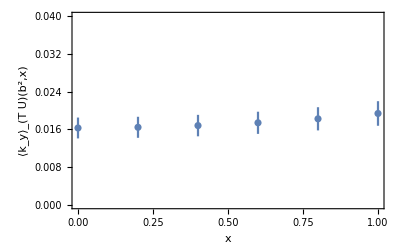

```mathematica
SiversShift3[9,-1, 8]
```

Fitting:    -> () = {⟨-0.135(16)⟩_(2902J), ⟨1.61(35)⟩_(2902J), ⟨0.324(58)⟩_(2902J)}, chisquareDoF = 2.6916
 Fitting:    -> () = {⟨0.4471(57)⟩_(2902J), ⟨1.044(14)⟩_(2902J), ⟨0.4553(52)⟩_(2902J)}, chisquareDoF = 55.1285
 Fitting:   -> () = {⟨0.0320(31)⟩_(2902J), ⟨1.04(17)⟩_(2902J), ⟨0.184(39)⟩_(2902J)} chisquareDoF = 2.67066
  = 9  = -2 ,eta = 8

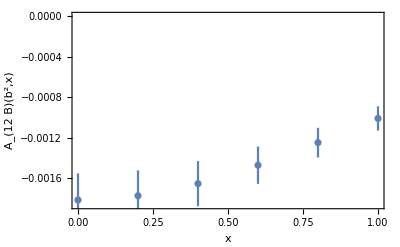

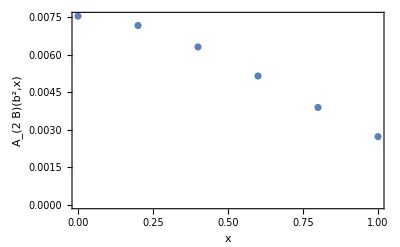

Sivers shift in GeV

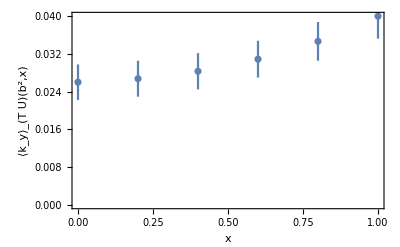

```mathematica
SiversShift3[9,-2, 8]
```

```mathematica
SiversShift3[9,-3, 8]
```

```mathematica
SiversShift3[9,-4, 8]
```

Fitting:    -> () = {⟨-0.030(47)⟩_(2902J), ⟨0.5 ± 1.3⟩_(2902J), ⟨0.47(31)⟩_(2902J)}, chisquareDoF = 0.34983
 Fitting:    -> () = {⟨0.391(23)⟩_(2902J), ⟨0.873(41)⟩_(2902J), ⟨0.579(31)⟩_(2902J)}, chisquareDoF = 3.83189
 Fitting:   -> () = {⟨0.053(12)⟩_(2902J), ⟨0.90(40)⟩_(2902J), ⟨0.48(15)⟩_(2902J)} chisquareDoF = 0.577557
  = 9  = -4 ,eta = 8

$Aborted

```mathematica
SiversShiftLLbT3Removed[b2_,P1_, etavalue_]:=Module[{dataforfitA12B, dataforfitA2B, fitJKA12B, fitParasA12B, chisqfitA12B, fitJKA2B, fitParasA2B, chisqfitA2B, fitJKImA2B, fitParasImA2B, chisqfitImA2B},
dataforfitA12B = MemDBGet[AmpDB,MemDBSelect[AmpDB,{A->A12B,PL->P1,etav->etavalue, bNum->even}],{bL, bT,data}];
dataforfitA2B = MemDBGet[AmpDB,MemDBSelect[AmpDB,{A->A2B,PL->P1,etav->etavalue, bNum->even}],{bL, bT,data}];
dataforfitImA2BFull = MemDBGet[AmpDB,MemDBSelect[AmpDB,{A->A2B,PL->P1,etav->etavalue, bNum->odd}],{bL, bT,data}];
Print[" for  are all removed!"];
dataforfitA2B=Select[dataforfitA2B,Abs[#[[2]]]>=1&];
dataforfitA12B=Select[dataforfitA12B,Abs[#[[2]]]>=1&];
dataforfitImA2B = Select[dataforfitImA2BFull,Abs[#[[2]]]>=1&];
modelfitA12B[x1_,x2_,{a_,b_,c_}]:=a*(1/((x1^2)+b))*(1/((x2^2)+c));
modelfitA2B[x1_,x2_,{a_,b_,c_}]:=a*(1/((x1^2)+b))*(1/((x2^2)+c));
modelfitImA2B[x1_,x2_,{a_,b_,c_}]:=a*x1*(1/((x1^2)+b))*(1/((x2^2)+c));
fitJKA12B =JackknifeFit3D[dataforfitA12B,modelfitA12B[bP,bsq,{a,b,c}],{a,b, c},{bP,bsq}, modelfitA12B];
fitParasA12B=FitParameters/. fitJKA12B;
chisqfitA12B=chisquareDoF/. fitJKA12B;
fitJKA2B =JackknifeFit3D[dataforfitA2B,modelfitA2B[bP,bsq,{a,b,c}],{a,b, c},{bP,bsq}, modelfitA2B];
fitParasA2B=FitParameters/. fitJKA2B;
chisqfitA2B=chisquareDoF/. fitJKA2B;
fitJKImA2B =JackknifeFit3D[dataforfitImA2B,modelfitImA2B[bP,bsq,{a,b,c}],{a,b, c},{bP,bsq}, modelfitImA2B];
fitParasImA2B=FitParameters/. fitJKImA2B;
chisqfitImA2B=chisquareDoF/. fitJKImA2B;
Print["Fitting:    -> () = ",OutputForm[fitParasA12B], ", chisquareDoF = ", chisqfitA12B,"\n Fitting:    -> () = ",OutputForm[fitParasA2B], ", chisquareDoF = ", chisqfitA2B, "\n Fitting:   -> () = ",OutputForm[fitParasImA2B]," chisquareDoF = ", chisqfitImA2B, "\n  = ",b2, "  = ",P1," ,eta = ", etavalue];
b2II = b2*fitParasA12B[[1]]/fitParasA12B[[1]];
II= fitParasA12B[[1]]/fitParasA12B[[1]];
fitaA12B =fitParasA12B[[1]];
fitbA12B=fitParasA12B[[2]];
fitcA12B =fitParasA12B[[3]];
fitaA2B =fitParasA2B[[1]];
fitbA2B=fitParasA2B[[2]];
fitcA2B =fitParasA2B[[3]];
fitaImA2B =fitParasImA2B[[1]];
fitbImA2B=fitParasImA2B[[2]];
fitcImA2B =fitParasImA2B[[3]];
MassN = MemDBGet[AmpDBPbbsq,MemDBSelect[AmpDBPbbsq,{A->A12B,PL->P1,etav->etavalue, bNum->even}],MN][[1]];
(*reducedratioA12B=(fitaA12B/(fitcA12B+b2II))*(II/(2*fitbA12B));
fourierA12B[x_, {reducedr_, bA12B_, cA12B_}] :=Sech[((N[Pi]*x)/(2*bA12B))]*reducedr;
reducedratioA2B=(fitaA2B/(fitcA2B+b2II))*(II/(2*fitbA2B));
reducedratioImA2B=(fitaImA2B/(fitcImA2B+b2II))*(II/(2*Sqrt[2]*(fitbImA2B)^(3/2)));
fourierA2B[x_, {reducedr_, bA2B_, bImA2B_}] :=Sech[((N[Pi]*x)/(2*bA2B))]*reducedr;
(*Print[reducedratioImA2B];*)
fourierImA2B[x_, {reducedr_, bA2B_, cA2B_}] :=x*Exp[-(x^2)/(4*bA2B)]*reducedr;
(*reducedratio1 = -MassN*(197*0.0001/lata)*reducedratioA12B/reducedratioA2B;
siversratio[x_, {reducedr1_, bA12B_, bA2B_}] := reducedr1*(Sech[((N[Pi]*x)/(2*bA12B))]/Sech[((N[Pi]*x)/(2*bA2B))]);*)*)
massterm=-MassN[[1]]*(197*0.0001/lata);
siversshiftxforplot={};
fourieA12Bxforplot={};
fourieA2Bxforplot={};
Do[
(*siversrforx = modelfitJackkifex[siversratio,{reducedratio1, fitbA12B, fitbA2B}, x];*)
modelReA12BNfou[pb_, jknum_]:=fitaA12B[[jknum]]*1/(fitbA12B[[jknum]]+((pb^2)/(P1^2)))*1/(fitcA12B[[jknum]]+(b2^2+((pb^2)/(P1^2))));
modelReA2BNfou[pb_, jknum_]:=fitaA2B[[jknum]]*1/(fitbA2B[[jknum]]+((pb^2)/(P1^2)))*1/(fitcA2B[[jknum]]+(b2^2+((pb^2)/(P1^2))));
modelImA2BNfou[pb_, jknum_]:=fitaImA2B[[jknum]]*((pb)/(-P1))*1/(fitbImA2B[[jknum]]+((pb^2)/(P1^2)))*1/(fitcImA2B[[jknum]]+(b2^2+((pb^2)/(P1^2))));
fourierA12Bforx = NFourierTransformJK[modelReA12BNfou,pb,x, Re];
fourierREA2Bforx=NFourierTransformJK[modelReA2BNfou,pb,x, Re];
fourierIMA2Bforx=NFourierTransformJK[modelImA2BNfou,pb,x, Im];
fourierA2Bforx=fourierREA2Bforx-fourierIMA2Bforx;
siversrforx=massterm*fourierA12Bforx/fourierA2Bforx;
AppendTo[siversshiftxforplot,{x,siversrforx}];
AppendTo[fourieA12Bxforplot,{x,fourierA12Bforx}];
AppendTo[fourieA2Bxforplot,{x,fourierA2Bforx}];
,{x,0,1, 0.2}];
MkErrA12B=MakeErrBars[fourieA12Bxforplot];
A12BPltrangMin=(MkErrA12B[[1]][[1]][[2]]+MkErrA12B[[1]][[2]][[1]][[1]])*0.5;
A12BPltrangMax=(MkErrA12B[[1]][[1]][[2]]+MkErrA12B[[1]][[2]][[1]][[2]])*1.5;
PlotfourieA12Bx = ErrorListPlot[MkErrA12B,FrameLabel->{ , }, Frame->True , PlotRange->{{Automatic,Automatic},{0,A12BPltrangMax}}];(* {{Automatic,Automatic},{0,0.0004}}*)
Print[PlotfourieA12Bx];
MkErrA2B=MakeErrBars[fourieA2Bxforplot];
A2BPltrangMin=(MkErrA2B[[1]][[1]][[2]]+MkErrA2B[[1]][[2]][[1]][[1]])*0.5;
A2BPltrangMax=(MkErrA2B[[1]][[1]][[2]]+MkErrA2B[[1]][[2]][[1]][[2]])*2;
PlotfourieA2Bx= ErrorListPlot[MkErrA2B,FrameLabel->{ , }, Frame->True , PlotRange->Full];(*{{Automatic,Automatic},{0.0045,0.0055}}*)
Print[PlotfourieA2Bx];
Print["Sivers shift in GeV"];
MkErrsiversshift=MakeErrBars[siversshiftxforplot];
SsPltrangMin=(MkErrsiversshift[[1]][[1]][[2]]-MkErrsiversshift[[1]][[2]][[1]][[1]])*0.5;
SsPltrangMax=(MkErrsiversshift[[1]][[1]][[2]]-MkErrsiversshift[[1]][[2]][[1]][[2]])*1.2;
Plotsivershift = ErrorListPlot[MkErrsiversshift,FrameLabel->{ , }, Frame->True , PlotRange->{{Automatic,Automatic},{0,0.09}}];(* PlotRange->{{Automatic,Automatic},{-0.3,0}}*)
Print[Plotsivershift];
(*Export["/Users/hariprashadravikumar/Downloads/Lorentz_bL_Lorentz_bT_Fourierx_A12B_"<>ToString[ampname]<>"_b_"<>ToString[bnum]<>"_P1_"<>ToString[P1]<>"_eta_"<>ToString[etavalue]<>".pdf",PlotfourieA12Bx,"PDF",ImageResolution->600];
Export["/Users/hariprashadravikumar/Downloads/Lorentz_bL_Lorentz_bT_Fourierx_A2B_"<>ToString[ampname]<>"_b_"<>ToString[bnum]<>"_P1_"<>ToString[P1]<>"_eta_"<>ToString[etavalue]<>".pdf",PlotfourieA2Bx,"PDF",ImageResolution->600];
Export["/Users/hariprashadravikumar/Downloads/Lorentz_bL_Lorentz_bT_Fourierx_SiversShift_"<>ToString[ampname]<>"_b_"<>ToString[bnum]<>"_P1_"<>ToString[P1]<>"_eta_"<>ToString[etavalue]<>".pdf",Plotsivershift,"PDF",ImageResolution->600];*)
];
```

for  are all removed!

Fitting:    -> () = {⟨-0.110(29)⟩_(2902J), ⟨2.36(51)⟩_(2902J), ⟨-0.03 ± 0.14⟩_(2902J)}, chisquareDoF = 1.72777
 Fitting:    -> () = {⟨0.2332(47)⟩_(2902J), ⟨1.039(11)⟩_(2902J), ⟨-0.031(14)⟩_(2902J)}, chisquareDoF = 86.1285
 Fitting:   -> () = {⟨0.0337(67)⟩_(2902J), ⟨0.54(14)⟩_(2902J), ⟨2.08(53)⟩_(2902J)} chisquareDoF = 1.45644
  = 9  = -1 ,eta = 9

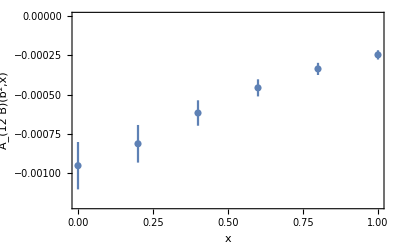

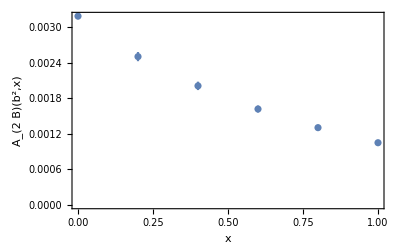

Sivers shift in GeV

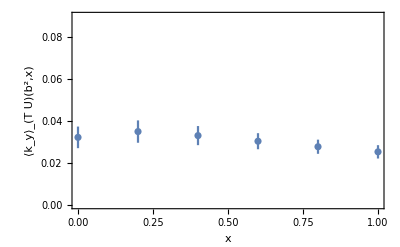

```mathematica
SiversShiftLLbT3Removed[9,-1, 9]
```

for  are all removed!

Fitting:    -> () = {⟨-0.072(18)⟩_(2902J), ⟨2.08(40)⟩_(2902J), ⟨-0.17(12)⟩_(2902J)}, chisquareDoF = 1.79704
 Fitting:    -> () = {⟨0.1583(53)⟩_(2902J), ⟨1.000(15)⟩_(2902J), ⟨-0.253(19)⟩_(2902J)}, chisquareDoF = 30.0571
 Fitting:   -> () = {⟨0.0291(59)⟩_(2902J), ⟨0.46(13)⟩_(2902J), ⟨0.71(25)⟩_(2902J)} chisquareDoF = 1.69552
  = 9  = -2 ,eta = 9

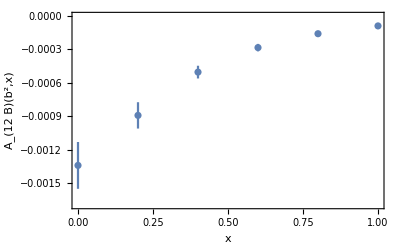

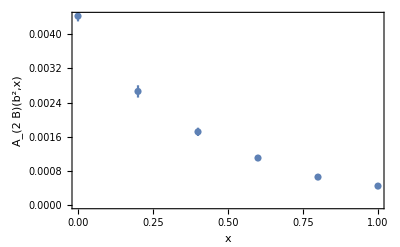

Sivers shift in GeV

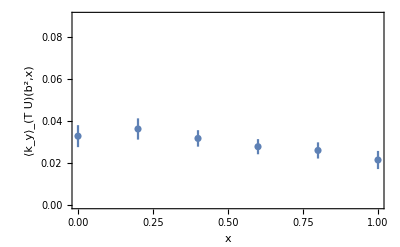

```mathematica
SiversShiftLLbT3Removed[9,-2, 9]
```

for  are all removed!

Fitting:    -> () = {⟨-0.037(22)⟩_(2902J), ⟨1.80(75)⟩_(2902J), ⟨-0.38(20)⟩_(2902J)}, chisquareDoF = 0.822023
 Fitting:    -> () = {⟨0.1153(82)⟩_(2902J), ⟨0.939(26)⟩_(2902J), ⟨-0.368(34)⟩_(2902J)}, chisquareDoF = 7.69987
 Fitting:   -> () = {⟨0.0202(79)⟩_(2902J), ⟨0.51(21)⟩_(2902J), ⟨0 ± 0.28⟩_(2902J)} chisquareDoF = 0.643222
  = 9  = -3 ,eta = 9

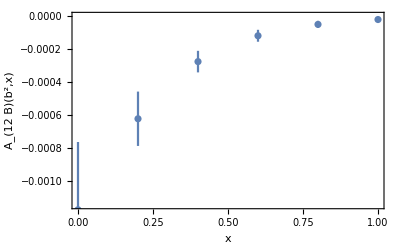

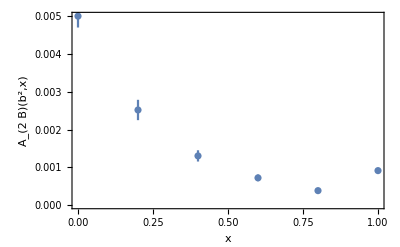

Sivers shift in GeV

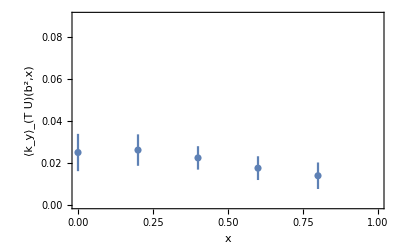

```mathematica
SiversShiftLLbT3Removed[9,-3, 9]
```

```mathematica
SiversShiftGLbT3Removed[b2_,P1_, etavalue_]:=Module[{dataforfitA12B, dataforfitA2B, fitJKA12B, fitParasA12B, chisqfitA12B, fitJKA2B, fitParasA2B, chisqfitA2B, fitJKImA2B, fitParasImA2B, chisqfitImA2B},
dataforfitA12B = MemDBGet[AmpDB,MemDBSelect[AmpDB,{A->A12B,PL->P1,etav->etavalue, bNum->even}],{bL, bT,data}];
dataforfitA2B = MemDBGet[AmpDB,MemDBSelect[AmpDB,{A->A2B,PL->P1,etav->etavalue, bNum->even}],{bL, bT,data}];
dataforfitImA2BFull = MemDBGet[AmpDB,MemDBSelect[AmpDB,{A->A2B,PL->P1,etav->etavalue, bNum->odd}],{bL, bT,data}];
Print[" for  are all removed!"];
dataforfitA2B=Select[dataforfitA2B,Abs[#[[2]]]>=1&];
dataforfitA12B=Select[dataforfitA12B,Abs[#[[2]]]>=1&];
dataforfitImA2B = Select[dataforfitImA2BFull,Abs[#[[2]]]>=1&];
dataforfitImA2B = Select[dataforfitImA2BFull,#[[2]]!=0&];
modelfitA12B[x1_,x2_,{a_,b_,c_}]:=a*Exp[(-b*x1^2)]*(1/((x2^2)+c));
modelfitA2B[x1_,x2_,{a_,b_,c_}]:=a*Exp[(-b*x1^2)]*(1/((x2^2)+c));
modelfitImA2B[x1_,x2_,{a_,b_,c_}]:=a*x1*Exp[(-b*x1^2)]*(1/((x2^2)+c));
fitJKA12B =JackknifeFit3D[dataforfitA12B,modelfitA12B[bP,bsq,{a,b,c}],{a,b, c},{bP,bsq}, modelfitA12B];
fitParasA12B=FitParameters/. fitJKA12B;
chisqfitA12B=chisquareDoF/. fitJKA12B;
fitJKA2B =JackknifeFit3D[dataforfitA2B,modelfitA2B[bP,bsq,{a,b,c}],{a,b, c},{bP,bsq}, modelfitA2B];
fitParasA2B=FitParameters/. fitJKA2B;
chisqfitA2B=chisquareDoF/. fitJKA2B;
fitJKImA2B =JackknifeFit3D[dataforfitImA2B,modelfitImA2B[bP,bsq,{a,b,c}],{a,b, c},{bP,bsq}, modelfitImA2B];
fitParasImA2B=FitParameters/. fitJKImA2B;
chisqfitImA2B=chisquareDoF/. fitJKImA2B;
Print["Fitting:    -> () = ",OutputForm[fitParasA12B], ", chisquareDoF = ", chisqfitA12B,"\n Fitting:    -> () = ",OutputForm[fitParasA2B], ", chisquareDoF = ", chisqfitA2B, "\n Fitting:   -> () = ",OutputForm[fitParasImA2B]," chisquareDoF = ", chisqfitImA2B, "\n  = ",b2, "  = ",P1," ,eta = ", etavalue];
b2II = b2*fitParasA12B[[1]]/fitParasA12B[[1]];
II= fitParasA12B[[1]]/fitParasA12B[[1]];
fitaA12B =fitParasA12B[[1]];
fitbA12B=fitParasA12B[[2]];
fitcA12B =fitParasA12B[[3]];
fitaA2B =fitParasA2B[[1]];
fitbA2B=fitParasA2B[[2]];
fitcA2B =fitParasA2B[[3]];
fitaImA2B =fitParasImA2B[[1]];
fitbImA2B=fitParasImA2B[[2]];
fitcImA2B =fitParasImA2B[[3]];
MassN = MemDBGet[AmpDBPbbsq,MemDBSelect[AmpDBPbbsq,{A->A12B,PL->P1,etav->etavalue, bNum->even}],MN][[1]];
massterm=-MassN[[1]]*(197*0.0001/lata);
siversshiftxforplot={};
fourieA12Bxforplot={};
fourieA2Bxforplot={};
Do[
(*siversrforx = modelfitJackkifex[siversratio,{reducedratio1, fitbA12B, fitbA2B}, x];*)
modelReA12BNfou[pb_, jknum_]:=fitaA12B[[jknum]]*Exp[(-fitbA12B[[jknum]]*((pb^2)/(P1^2)))]*1/(fitcA12B[[jknum]]+(b2^2+((pb^2)/(P1^2))));
modelReA2BNfou[pb_, jknum_]:=fitaA2B[[jknum]]*Exp[(-fitbA2B[[jknum]]*((pb^2)/(P1^2)))]*1/(fitcA2B[[jknum]]+(b2^2+((pb^2)/(P1^2))));
modelImA2BNfou[pb_, jknum_]:=fitaImA2B[[jknum]]*((pb)/(-P1))*Exp[(-fitbImA2B[[jknum]]*((pb^2)/(P1^2)))]*1/(fitcImA2B[[jknum]]+(b2^2+((pb^2)/(P1^2))));
fourierA12Bforx = NFourierTransformJK[modelReA12BNfou,pb,x, Re];
fourierREA2Bforx=NFourierTransformJK[modelReA2BNfou,pb,x, Re];
fourierIMA2Bforx=NFourierTransformJK[modelImA2BNfou,pb,x, Im];
fourierA2Bforx=fourierREA2Bforx-fourierIMA2Bforx;
siversrforx=massterm*fourierA12Bforx/fourierA2Bforx;
AppendTo[siversshiftxforplot,{x,siversrforx}];
AppendTo[fourieA12Bxforplot,{x,fourierA12Bforx}];
AppendTo[fourieA2Bxforplot,{x,fourierA2Bforx}];
,{x,0,1, 0.2}];
MkErrA12B=MakeErrBars[fourieA12Bxforplot];
A12BPltrangMin=(MkErrA12B[[1]][[1]][[2]]+MkErrA12B[[1]][[2]][[1]][[1]])*0.5;
A12BPltrangMax=(MkErrA12B[[1]][[1]][[2]]+MkErrA12B[[1]][[2]][[1]][[2]])*1.2;
PlotfourieA12Bx = ErrorListPlot[MkErrA12B,FrameLabel->{ , }, Frame->True , PlotRange->{{Automatic,Automatic},{0,A12BPltrangMax}}];(* {{Automatic,Automatic},{0,0.0004}}*)
Print[PlotfourieA12Bx];
MkErrA2B=MakeErrBars[fourieA2Bxforplot];
A2BPltrangMin=(MkErrA2B[[1]][[1]][[2]]+MkErrA2B[[1]][[2]][[1]][[1]])*0.5;
A2BPltrangMax=(MkErrA2B[[1]][[1]][[2]]+MkErrA2B[[1]][[2]][[1]][[2]])*2;
PlotfourieA2Bx= ErrorListPlot[MkErrA2B,FrameLabel->{ , }, Frame->True , PlotRange->Full];(*{{Automatic,Automatic},{0.0045,0.0055}}*)
Print[PlotfourieA2Bx];
Print["Sivers shift in GeV"];
MkErrsiversshift=MakeErrBars[siversshiftxforplot];
SsPltrangMin=(MkErrsiversshift[[1]][[1]][[2]]-MkErrsiversshift[[1]][[2]][[1]][[1]])*0.5;
SsPltrangMax=(MkErrsiversshift[[1]][[1]][[2]]-MkErrsiversshift[[1]][[2]][[1]][[2]])*1.2;
Plotsivershift = ErrorListPlot[MkErrsiversshift,FrameLabel->{ , }, Frame->True , PlotRange->{{Automatic,Automatic},{0,0.04}}];(* PlotRange->{{Automatic,Automatic},{-0.3,0}}*)
Print[Plotsivershift];
(*Export["/Users/hariprashadravikumar/Downloads/Gaussian_bL_Lorentz_bT_Fourierx_A12B_"<>ToString[ampname]<>"_b_"<>ToString[bnum]<>"_P1_"<>ToString[P1]<>"_eta_"<>ToString[etavalue]<>".pdf",PlotfourieA12Bx,"PDF",ImageResolution->600];
Export["/Users/hariprashadravikumar/Downloads/Gaussian_bL_Lorentz_bT_Fourierx_A2B_"<>ToString[ampname]<>"_b_"<>ToString[bnum]<>"_P1_"<>ToString[P1]<>"_eta_"<>ToString[etavalue]<>".pdf",PlotfourieA2Bx,"PDF",ImageResolution->600];
Export["/Users/hariprashadravikumar/Downloads/Gaussian_bL_Lorentz_bT_Fourierx_SiversShift_"<>ToString[ampname]<>"_b_"<>ToString[bnum]<>"_P1_"<>ToString[P1]<>"_eta_"<>ToString[etavalue]<>".pdf",Plotsivershift,"PDF",ImageResolution->600];*)
];
```

for  are all removed!

Fitting:    -> () = {⟨-0.0442(53)⟩_(2902J), ⟨0.169(40)⟩_(2902J), ⟨0.07 ± 0.16⟩_(2902J)}, chisquareDoF = 1.46828
 Fitting:    -> () = {⟨0.2043(29)⟩_(2902J), ⟨0.3785(31)⟩_(2902J), ⟨0.025(14)⟩_(2902J)}, chisquareDoF = 80.9168
 Fitting:   -> () = {⟨0.0220(32)⟩_(2902J), ⟨0.175(18)⟩_(2902J), ⟨2.23(51)⟩_(2902J)} chisquareDoF = 1.41277
  = 9  = -1 ,eta = 9

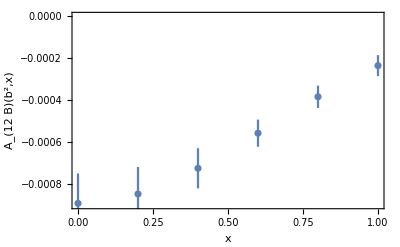

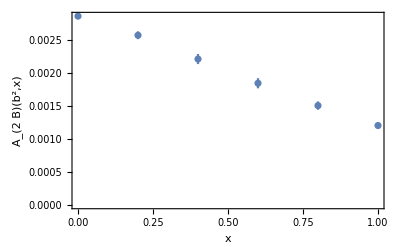

Sivers shift in GeV

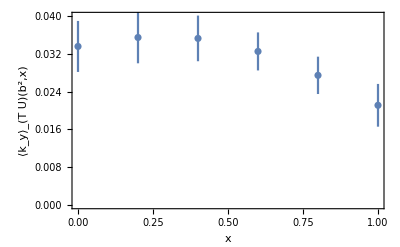

```mathematica
SiversShiftGLbT3Removed[9,-1, 9]
```

for  are all removed!

Fitting:    -> () = {⟨-0.0334(39)⟩_(2902J), ⟨0.204(39)⟩_(2902J), ⟨-0.10(13)⟩_(2902J)}, chisquareDoF = 1.44679
 Fitting:    -> () = {⟨0.1446(37)⟩_(2902J), ⟨0.3811(43)⟩_(2902J), ⟨-0.200(19)⟩_(2902J)}, chisquareDoF = 19.7438
 Fitting:   -> () = {⟨0.0209(30)⟩_(2902J), ⟨0.205(26)⟩_(2902J), ⟨0.68(25)⟩_(2902J)} chisquareDoF = 1.57558
  = 9  = -2 ,eta = 9

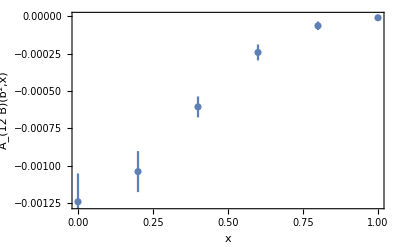

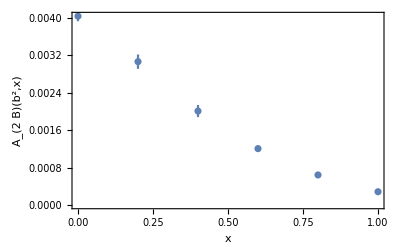

Sivers shift in GeV

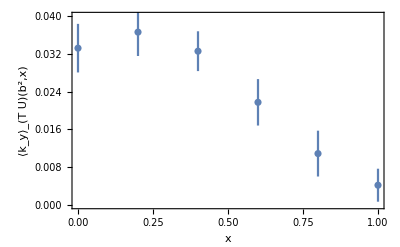

```mathematica
SiversShiftGLbT3Removed[9,-2, 9]
```

for  are all removed!

Fitting:    -> () = {⟨-0.0209(52)⟩_(2902J), ⟨0.211(91)⟩_(2902J), ⟨-0.30(23)⟩_(2902J)}, chisquareDoF = 0.757793
 Fitting:    -> () = {⟨0.1124(61)⟩_(2902J), ⟨0.3978(86)⟩_(2902J), ⟨-0.318(36)⟩_(2902J)}, chisquareDoF = 3.85721
 Fitting:   -> () = {⟨0.0140(43)⟩_(2902J), ⟨0.189(37)⟩_(2902J), ⟨0.009 ± 0.29⟩_(2902J)} chisquareDoF = 0.680181
  = 9  = -3 ,eta = 9

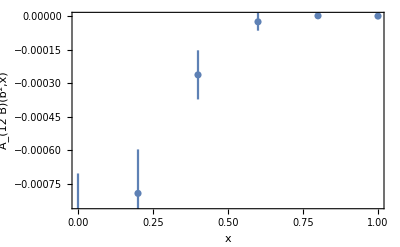

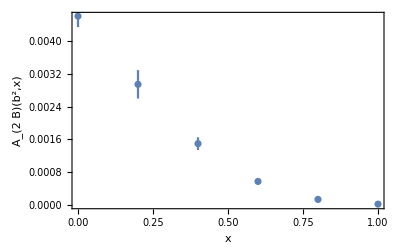

Sivers shift in GeV

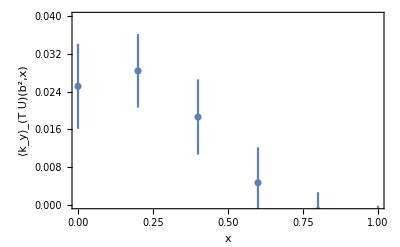

```mathematica
SiversShiftGLbT3Removed[9,-3, 9]
```